```mathematica
SI Appendix for Indirect reciprocity with Bayesian reasoning
B. Morsky, J. Plotkin, E. Akçay
```

```mathematica
SetDirectory["/Users/brycemorsky/Desktop/New projects/Indirect reciprocity/figures"];
```

## Scoring

```mathematica
Clear["Global`*"]
pix=r*(x+Qcg*z)-1;
piy=r*(x+Qdg*z);
piz=r*(x+(g*Qcg+(1-g)*Qdg)*z)-g;
pibar=x*pix+(1-x-z)*piy+z*piz;
FullSimplify[(pix-pibar)*x]
FullSimplify[(piy-pibar)*y]
FullSimplify[(piz-pibar)*z]
```

-x (-1+x+g z) (-1+(Qcg-Qdg) r z)

-y (x+g z) (-1+(Qcg-Qdg) r z)

-(x+g (-1+z)) z (-1+(Qcg-Qdg) r z)

```mathematica
Clear["Global`*"]
Pc=ϵ*g/(ϵ*g+e*(1-g));
Pd=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Qc=ϵ*Pc+(1-ϵ)*Pd;
Qd=(1-e)*Pd+e*Pc;
(* gz=g with no bias *)
FullSimplify[Qc*g+Qd*(1-g)]
```

g

### Theorem A.1.1

```mathematica
(* Equilibrium g of the reputation system in the interior of the simplex *)
{fx,fy,fz}={Qc-gx,Qd-gy,Qc*g+Qd*(1-g)-gz};
FullSimplify[g-x*Qc-y*Qd-(1-x-y)*(g*Qc+(1-g)*Qd)]
Solve[g==x*Qc+y*Qd+(1-x-y)*(Qc*g+Qd*(1-g)),g]
(* Eigenvalues of the Jacobian for equilibrium g=0 in the interior of the simplex *)
FullSimplify[Eigenvalues[D[{fx,fy,fz}/.{g->gx*x+gy*y+gz*(1-x-y)},{{gx,gy,gz}}]/.{gx->0,gy->0,gz->0}]]
(* Eigenvalues of the Jacobian for equilibrium g=1 in the interior of the simplex *)
FullSimplify[Eigenvalues[D[{fx,fy,fz}/.{g->gx*x+gy*y+gz*(1-x-y)},{{gx,gy,gz}}]/.{gx->1,gy->1,gz->1}]]
(* Equilibria gx, gy, and gz, and eigenvalues of the Jacobian for equilibrium g=x/x+y in the interior of the simplex *)
gxeq=FullSimplify[Qc/.{g->x/(x+y)}]
gyeq=FullSimplify[Qd/.{g->x/(x+y)}]
gzeq=FullSimplify[Qc*g+Qd*(1-g)/.{g->x/(x+y)}]
FullSimplify[Eigenvalues[D[{fx,fy,fz}/.{g->gx*x+gy*y+gz*(1-x-y)},{{gx,gy,gz}}]/.{gx->gxeq,gy->gyeq,gz->gzeq}]]
(* Show dz/dt = 0 *)
pix=r*(x+Qcg*z)-1;
piy=r*(x+Qdg*z);
piz=r*(x+(g*Qcg+(1-g)*Qdg)*z)-g;
pibar=x*pix+(1-x-z)*piy+z*piz;
FullSimplify[(piz-pibar)*z]
(* Equilibrium g of the reputation system on the AllC-Disc boundary *)
FullSimplify[g-x*Qc-(1-x)*(g*Qc+(1-g)*Qd)]
Solve[g==x*Qc+(1-x)*(Qc*g+Qd*(1-g)),g]
(* Eigenvalues of the Jacobian for equilibrium g=0 on the AllC-Disc boundary *)
FullSimplify[Eigenvalues[D[{fx,fz}/.{g->gx*x+gz*(1-x)},{{gx,gz}}]/.{gx->0,gz->0}]]
(* Equilibrium g of the reputation system on the AllD-Disc boundary *)
FullSimplify[g-y*Qd-(1-y)*(g*Qc+(1-g)*Qd)]
Solve[g==y*Qd+(1-y)*(Qc*g+Qd*(1-g)),g]
(* Eigenvalues of the Jacobian for equilibrium g=1 on the AllD-Disc boundary *)
FullSimplify[Eigenvalues[D[{fy,fz}/.{g->gy*y+gz*(1-y)},{{gy,gz}}]/.{gy->1,gz->1}]]
```

### Theorem A.1.2

```mathematica
(* Simplify r*z*(Qc-Qd)-1 at g=x/(1-z)*)
sol=FullSimplify[r*z*(Qc-Qd)-1/.{g->x/(1-z)}]
(* Collect coefficients for numerator of r*z*(Qc-Qd)-1, note we take the negative of sol, since the denominator is negative *)
FullSimplify[CoefficientList[Numerator[-sol],x]]
(* r*z*(Qc-Qd)-1 = -1 when x=0 or 1 *)
FullSimplify[r*z*(Qc-Qd)-1//.{g->0,x->0}]
FullSimplify[r*z*(Qc-Qd)-1//.{g->1,x->1}]
```

(e (-1+x+z) (-1+e+z-e z+e x (-1+r z))-x (-1+z+2 e (-1+x+z) (-1+r z)) ϵ+x (r (-1+z) z+x (-1+r z)) ϵ^2)/((e (-1+x+z)-x ϵ) (1-z+e (-1+x+z)-x ϵ))

{(-1+e) e (-1+z)^2,-(-1+z) (e-ϵ) (1+e (-2+r z)-r z ϵ),-(-1+r z) (e-ϵ)^2}

-1

-1

```mathematica
(* d(Qcg-Qdg)/de1 < 0 and d(Qcg-Qdg)/de2 < 0 *)
FullSimplify[D[Evaluate[Qc-Qd/.{ϵ->(1-e1)*(1-e2)+e1*e2,e->e2}],e1]]
FullSimplify[D[Evaluate[Qc-Qd/.{ϵ->(1-e1)*(1-e2)+e1*e2,e->e2}],e2]]
```

((-1+e1) (1-2 e2)^2 (-1+g) g (2 (-1+e2) e2+(-1+e1) (1-2 e2)^2 g))/((-1+e2+(-1+e1) (-1+2 e2) g)^2 (e2+(-1+e1) (-1+2 e2) g)^2)

-((-1+e1)^2 (-1+2 e2) (-1+g) g)/((-1+e2+(-1+e1) (-1+2 e2) g)^2 (e2+(-1+e1) (-1+2 e2) g)^2)

## Simple Standing

```mathematica
Clear["Global`*"]
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=1;
Qdb=1;
```

### Lemma A.3.1

```mathematica
(* Calculate (dQcg/dg)*g*z + (dQdg/dg)*g*(1-z) - 1 for 0≤g<1 *)
FullSimplify[D[Qdg,g]*g*(1-z)+D[Qcg,g]*g*z-1/.{z->(2-1/g-Qdg)/(Qcg-Qdg)}]
(* Calculate (dQcg/dg)*g*z + (dQdg/dg)*g*(1-z) - 1 for g=1 *)
FullSimplify[D[Qdg,g]*g*(1-z)+D[Qcg,g]*g*z-1/.{g->1}]
```

-((-1+g) (e^2 (-1+g+g^2)+g^2 ϵ^2-e (-1+g+2 g^2 ϵ)))/(g (e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

((-1+z) (e-ϵ)^2)/((-1+ϵ) ϵ)

### Theorem A.3.2

```mathematica
(* Simplify g - x*gx - y*gy - z*gz = 0 *)
FullSimplify[g-x*(Qcg*g+1-g)-y*(Qdg*g+1-g)-(1-x-y)*(Qcg*g+1-g)]
(* Quadratic polynomial in the numerator p(g) *)
p =(-e (-1+g)^2+e^2 (1+g (-3+g (2+y)))-2 e g (-1+g+g y) ϵ+g ϵ (-1+g+g y ϵ));
FullSimplify[CoefficientList[p,g]]
p/.{g->0}
p/.(g->1)
(* Characteristic equation *)
Clear["Global`*"]
FullSimplify[CharacteristicPolynomial[{{dQcg*g*x+(Qcg-1)*x-1,dQcg*g*y+(Qcg-1)*y,dQcg*g*(1-x-y)+(Qcg-1)*(1-x-y)},{dQdg*g*x+(Qdg-1)*x,dQdg*g*y+(Qdg-1)*y-1,dQdg*g*(1-x-y)+(Qdg-1)*(1-x-y)},{dQcg*g*x+(Qcg-1)*x,dQcg*g*y+(Qcg-1)*y,dQcg*g*(1-x-y)+(Qcg-1)*(1-x-y)-1}},λ]]
```

-1+g (2+Qcg (-1+y)-Qdg y)

{(-1+e) e,-ϵ+e (2-3 e+2 ϵ),(e-ϵ) (-1+e (2+y)-y ϵ)}

-e+e^2

e^2 y-2 e y ϵ+y ϵ^2

-(1+λ)^2 (2+dQcg g (-1+y)+Qcg (-1+y)-(dQdg g+Qdg) y+λ)

### Theorem A.3.4

```mathematica
(* The numerator of Qcg*g + 1-2*g *)
num=FullSimplify[(ϵ^2*hatg*((1-ϵ)*hatg+(1-e)*(1-hatg)) + (1-ϵ)^2*hatg*(ϵ*hatg+e*(1-hatg)))*g +(1-2*g)*((1-ϵ)*hatg+(1-e)*(1-hatg))*(ϵ*hatg+e*(1-hatg))/.ghat->(1-λ)*g+λ/.{hatg->(1-λ)*g+λ}]
(* Coefficients for polynomial *)
{c0,c1,c2}=FullSimplify[CoefficientList[FullSimplify[num/(1-g)],g]]
(* Polynomial at g=1 *)
FullSimplify[c2+c1+c0]
```

(-1+g) (e^2 (-1+g) (-1+2 g) (-1+λ)^2-e (-1+g) (-1+λ) (1+g (1+2 ϵ) (-1+λ)-2 ϵ λ)+ϵ (g (-1+λ)-λ) (1+g (-1+λ)-ϵ λ))

{-(e (-1+λ)-ϵ λ) (1+e (-1+λ)-ϵ λ),(-1+λ) (2 e-3 e^2-ϵ+2 e ϵ+(1-3 e+ϵ) (-e+ϵ) λ),-(-1+2 e) (e-ϵ) (-1+λ)^2}

-(-1+ϵ) ϵ λ

### Theorem A.3.8

```mathematica
Solve[g==((1-e)*Pdg+e*Pcg)*g+1-g,g]
```

{{g→1},{g→(-2 e+3 e^2+ϵ-2 e ϵ-√(4 e^3-3 e^4-6 e^2 ϵ+4 e^3 ϵ+ϵ^2))/(2 (-e+3 e^2+ϵ-4 e ϵ+ϵ^2))},{g→(-2 e+3 e^2+ϵ-2 e ϵ+√(4 e^3-3 e^4-6 e^2 ϵ+4 e^3 ϵ+ϵ^2))/(2 (-e+3 e^2+ϵ-4 e ϵ+ϵ^2))}}

```mathematica
test2=FullSimplify[Together[2*g-1-Qdg*g/.{Qdg->(1-e)*Pdg+e*Pcg }]]
```

((-1+g) (e^2 (1+3 (-1+g) g)+g ϵ (-1+g+g ϵ)-e (1+g (g+4 g ϵ-2 (1+ϵ)))))/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

```mathematica
Simplify[(-2 e+3 e^2+ϵ-2 e ϵ+√(4 e^3-3 e^4-6 e^2 ϵ+4 e^3 ϵ+ϵ^2))/(2 (-e+3 e^2+ϵ-4 e ϵ+ϵ^2))/.{ϵ->0.9802,e->0.01,z->0.6}]
```

0.507588

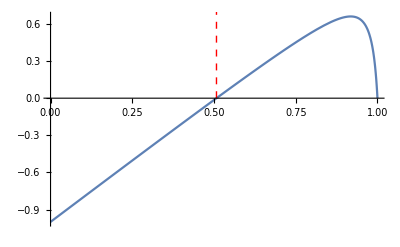

```mathematica
test=-1-g (-2+Qdg)-(Qcg-Qdg) (z*(1-z)*(Qdg*g+1-g)^2+(g-(1-z)*(Qdg*g+1-g))^2)/.{Qcg->ϵ*Pcg+(1-ϵ)*Pdg,Qdg->(1-e)*Pdg+e*Pcg};
line1=Line[{{0.5075884421069583,0},{0.5075884421069583,1}}];
Plot[Evaluate[test2/.{ϵ->0.9802,e->0.01,z->0.6}],{g,0,1},Epilog->{Directive[{Thick,Red,Dashed}],line1}]
```

```mathematica
FullSimplify[(2-Qdg)*g-1-(Qcg-Qdg)*(g-gy-(z*(1-z)*gy^2+(g-(1-z)*gy)^2)]
```

```mathematica
FullSimplify[g-g^2+gy (-1+gy (-1+z))-2 g gy (-1+z)/.{gy->Qdg*g+1-g}]
```

```mathematica
D[-2+z+g (-2+Qdg) (-3+2 z)+g^2 (-4+(-4+Qdg) Qdg (-1+z)+3 z),z]
```

1+2 g (-2+Qdg)+g^2 (3+(-4+Qdg) Qdg)

```mathematica
FullSimplify[(2-Qdg)*g-1-(Qcg-Qdg)(z*(1-z)*(Qdg*g+1-g)^2+(g-(1-z)*(Qdg*g+1-g))^2)]
```

-1-g (-2+Qdg)-(Qcg-Qdg) ((g+(1+g (-1+Qdg)) (-1+z))^2-(1+g (-1+Qdg))^2 (-1+z) z)

```mathematica
FullSimplify[D[-1-g (-2+Qdg)-(Qcg-Qdg) (z*(1-z)*(Qdg*g+1-g)^2+(g-(1-z)*(Qdg*g+1-g))^2),z]]
```

(1+g (-3+Qdg)) (1+g (-1+Qdg)) (Qcg-Qdg)

```mathematica
D[-1-g[z] (-2+Qdg[g[z]])-(Qcg[g[z]]-Qdg[g[z]]) ((1-y)*y*(Qdg[g[z]]*g[z]+1-g[z])^2+(g[z]-y*(Qdg[g[z]]*g[z]+1-g[z]))^2),z]
```

-(-2+Qdg[g[z]]) g'[z]-g[z] g'[z] Qdg'[g[z]]-((1-y) y (1-g[z]+g[z] Qdg[g[z]])^2+(g[z]-y (1-g[z]+g[z] Qdg[g[z]]))^2) (g'[z] Qcg'[g[z]]-g'[z] Qdg'[g[z]])-(Qcg[g[z]]-Qdg[g[z]]) (2 (1-y) y (1-g[z]+g[z] Qdg[g[z]]) (-g'[z]+Qdg[g[z]] g'[z]+g[z] g'[z] Qdg'[g[z]])+2 (g[z]-y (1-g[z]+g[z] Qdg[g[z]])) (g'[z]-y (-g'[z]+Qdg[g[z]] g'[z]+g[z] g'[z] Qdg'[g[z]])))

```mathematica
Simplify[(1+g (-3+Qdg)) (1+g (-1+Qdg)) (Qcg-Qdg)-(1+2 g (-2+Qdg)+g^2 (3+(-4+Qdg) Qdg))]
```

(-1+Qcg-Qdg) (1+2 g (-2+Qdg)+g^2 (3-4 Qdg+Qdg^2))

### Numerical convergence

```mathematica
(* Public *)
M=Array[m,{24*2,2}];
e1=0.01;
e=0.01;
ϵ=(1-e1)*(1-e)+e1*e;
Do[
z=0.01*i;
{fy,fz}={Qdg*g+1-g-gy,Qcg*g+1-g-gz}//.{g->(1-z)*gy+z*gz};
geq=Select[g/.Solve[g==(Qcg*g+1-g)*z+(Qdg*g+1-g)*(1-z),g],0<#<1&][[1]];
{gyeq,gzeq}={Qdg*g+1-g,Qcg*g+1-g}/.{g->geq};
eigs=Eigenvalues[D[{fy,fz},{{gy,gz}}]//.{g->geq,gy->gyeq,gz->gzeq}];M[[i/4]]={z,eigs[[1]]};
M[[i/4+24]]={z,eigs[[2]]};
,{i,4,96,4}]
eigenImage=ListPlot[M,LabelStyle->"20",ImageSize->Large,PlotStyle->{Directive[Blue,PointSize[Large]]},PlotMarkers->Automatic,BaseStyle->{FontSize->28},PlotRange->{{0,1},{-1.005,-0.96}},Frame->{{True,True},{True,True}},FrameStyle->{{Black,Black},{Black,Black}},AspectRatio->1,FrameLabel->{Framed[Style["Discriminators, z"],FrameStyle->None],"Eigenvalues"}];
Export["eigen_SS_public.pdf",eigenImage];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

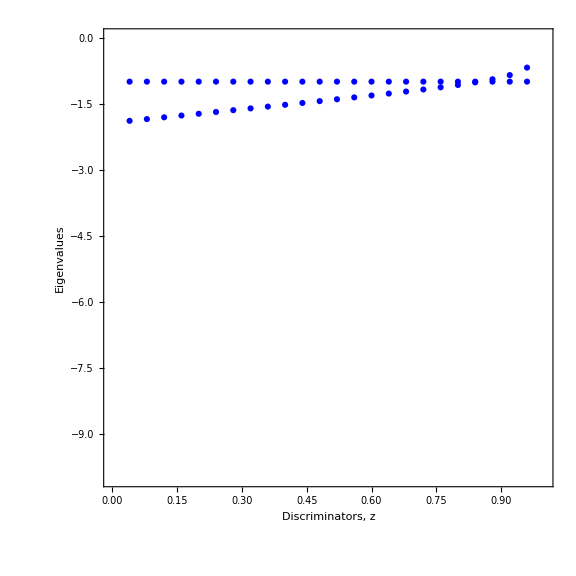

```mathematica
ListPlot[M,LabelStyle->"20",ImageSize->Large,PlotStyle->{Directive[Blue,PointSize[Large]]},PlotMarkers->Automatic,BaseStyle->{FontSize->28},PlotRange->{{0,1},{-10,0}},Frame->{{True,True},{True,True}},FrameStyle->{{Black,Black},{Black,Black}},AspectRatio->1,FrameLabel->{Framed[Style["Discriminators, z"],FrameStyle->None],"Eigenvalues"}]
```

```mathematica
(* Private *)
M=Array[m,{24*2,2}];
e1=1/100;
e=1/100;
ϵ=(1-e1)*(1-e)+e1*e;
Do[
z=i/100;
g=(1-z)*gy+z*gz;
g2=(1-z)gy2^2+z*gz2^2;
{fy,fz,fy2,fz2}={Qdg*g+1-g-gy,Qcg*g2+Qdg*(g-g2)+1-g-gz,gy^2-gy2,gz^2-gz2};
{gyeq,gzeq}=Select[Round[{gy,gz}/.Solve[{Qdg*g+1-g== gy,Qcg*((1-z)gy^2+z*gz^2)+Qdg*(g-((1-z)gy^2+z*gz^2))+1-g==gz},{gy,gz},Reals],0.0001],0<#[[1]]<1&&0<#[[2]]<1&][[1]];
eigs=Eigenvalues[D[{fy,fz,fy2,fz2},{{gy,gz,gy2,gz2}}]/.{gy2->gyeq^2,gz2->gzeq^2,gy->gyeq,gz->gzeq}];M[[i/4]]={z,eigs[[1]]};
M[[i/4+24]]={z,eigs[[2]]};
,{i,4,96,4}]
eigenImage=ListPlot[M,LabelStyle->"20",ImageSize->Large,PlotStyle->{Directive[Blue,PointSize[Large]]},PlotMarkers->Automatic,BaseStyle->{FontSize->28},PlotRange->{{0,1},{-3,-0.5}},Frame->{{True,True},{True,True}},FrameStyle->{{Black,Black},{Black,Black}},AspectRatio->1,FrameLabel->{Framed[Style["Discriminators, z"],FrameStyle->None],"Eigenvalues"}];
Export["eigen_SS_private.pdf",eigenImage];
```

## Staying

```mathematica
Clear["Global`*"]
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
```

### Theorem A.4.1

```mathematica
(* Equilibrium g of the reputation system in the interior of the AllD-Disc boundary is non-zero *)
{fx,fy,fz}={Qcg-gx,Qdg-gy,Qcg-gz};
FullSimplify[g-x*Qcg-y*Qdg-(1-x-y)*Qcg]
Solve[g==x*Qcg+y*Qdg+(1-x-y)*Qcg,g]
(* Eigenvalues of the Jacobian for equilibrium g=0 *)
FullSimplify[Eigenvalues[D[{fx,fy,fz}/.{g->x*gx+y*gy+gz*(1-x-y)},{{gx,gy,gz}}]/.{gx->0,gy->0,gz->0}]]
(* Eigenvalues of the Jacobian for equilibrium g=1 *)
FullSimplify[Eigenvalues[D[{fx,fy,fz}/.{g->x*gx+y*gy+gz*(1-x-y)},{{gx,gy,gz}}]/.{gx->1,gy->1,gz->1}]]
(* Eigenvalues of the Jacobian for equilibrium g=1-y *)
gxeq=FullSimplify[Qcg/.{g->1-y}];
gyeq=FullSimplify[Qdg/.{g->1-y}];
gzeq=FullSimplify[Qcg/.{g->1-y}];
FullSimplify[Eigenvalues[D[{fx,fy,fz}/.{g->x*gx+y*gy+gz*(1-x-y)},{{gx,gy,gz}}]/.{gx->gxeq,gy->gyeq,gz->gzeq}]]
```

((-1+g) g (-1+g+y) (e-ϵ)^2)/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

{{g→0},{g→1},{g→1-y}}

{-1,-1,((-1+y) (e-ϵ)^2)/((-1+e) e)}

{-(y (e-ϵ)^2)/((-1+ϵ) ϵ),-1,-1}

{-((-1+y) y (e-ϵ)^2)/((-1+e y+ϵ-y ϵ) (e y+ϵ-y ϵ)),-1,-1}

### Theorem A.4.3

```mathematica
(* Equilibrium g of the reputation system in the interior of the AllD-Disc boundary is non-zero *)
{fy,fz}={Qdg-gy,Qcg-gz};
FullSimplify[g-y*Qdg-(1-y)*Qcg]
Solve[g==y*Qdg+(1-y)*Qcg,g]
(* Eigenvalues of the Jacobian for equilibrium g=0 *)
FullSimplify[Eigenvalues[D[{fy,fz}/.{g->gy*y+gz*(1-y)},{{gy,gz}}]/.{gy->0,gz->0}]]
(* Eigenvalues of the Jacobian for equilibrium g=1 *)
FullSimplify[Eigenvalues[D[{fy,fz}/.{g->gy*y+gz*(1-y)},{{gy,gz}}]/.{gy->1,gz->1}]]
(* The numerator of Qcg*g + 1-2*g *)
num=FullSimplify[(ϵ^2*hatg*((1-ϵ)*hatg+(1-e)*(1-hatg)) + (1-ϵ)^2*hatg*(ϵ*hatg+e*(1-hatg)))*g +(1-2*g)*((1-ϵ)*hatg+(1-e)*(1-hatg))*(ϵ*hatg+e*(1-hatg))/.ghat->(1-λ)*g+λ/.{hatg->(1-λ)*g+λ}]
(* Coefficients for polynomial *)
{c0,c1,c2}=FullSimplify[CoefficientList[FullSimplify[num/(1-g)],g]]
(* Polynomial at g=1 *)
FullSimplify[c2+c1+c0]
```

((-1+g) g (-1+g+y) (e-ϵ)^2)/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

{{g→0},{g→1},{g→1-y}}

{-1,((-1+y) (e-ϵ)^2)/((-1+e) e)}

{-(y (e-ϵ)^2)/((-1+ϵ) ϵ),-1}

(-1+g) (e^2 (-1+g) (-1+2 g) (-1+λ)^2-e (-1+g) (-1+λ) (1+g (1+2 ϵ) (-1+λ)-2 ϵ λ)+ϵ (g (-1+λ)-λ) (1+g (-1+λ)-ϵ λ))

{-(e (-1+λ)-ϵ λ) (1+e (-1+λ)-ϵ λ),(-1+λ) (2 e-3 e^2-ϵ+2 e ϵ+(1-3 e+ϵ) (-e+ϵ) λ),-(-1+2 e) (e-ϵ) (-1+λ)^2}

-(-1+ϵ) ϵ λ

### Theorem A.4.4

```mathematica
(* Calculate (dQcg/dg)*z + (dQdg/dg)*(1-z) - 1 *)
FullSimplify[D[Qdg,g]*(1-z)+D[Qcg,g]*z-1/.{z->(g-Qdg)/(Qcg-Qdg)}]
```

-((-1+g) g (e-ϵ)^2)/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

### Theorem A.4.5

```mathematica
Clear["Global`*"]
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
(* Equilibrium g of the reputation system in the interior of the AllD-Disc boundary is non-zero *)
{fx,fy,fz,fx2,fy2,fz2}={Qcg*g-gx*g,Qdg*g-gy*g,(Qcg-Qdg)*g2+Qdg*g-gz*g,(gx^2-gx2)*g,(gy^2-gy2)*g,(gz^2-gz2)*g};
FullSimplify[g-x*Qcg-y*Qdg-(1-x-y)*((Qcg-Qdg)*g2/g+Qdg)]
Solve[g^2==x*Qcg*g+y*Qdg*g+(1-x-y)*((Qcg-Qdg)*g2+Qdg*g),g]
(* Eigenvalues of the Jacobian for equilibrium g=0 *)
FullSimplify[Eigenvalues[D[{fx,fy,fz,fx2,fy2,fz2}/.{g->x*gx+y*gy+(1-x-y)*gz,g2->x*gx2+y*gy2+(1-x-y)*gz2},{{gx,gy,gz,gx2,gy2,gz2}}]/.{gx->0,gy->0,gz->0,gx2->0,gy2->0,gz2->0}]]
(* Eigenvalues of the Jacobian for equilibrium g=1 *)
FullSimplify[Eigenvalues[D[{fx,fy,fz,fx2,fy2,fz2}/.{g->x*gx+y*gy+(1-x-y)*gz,g2->x*gx2+y*gy2+(1-x-y)*gz2},{{gx,gy,gz,gx2,gy2,gz2}}]/.{gx->1,gy->1,gz->1,gx2->1,gy2->1,gz2->1}]]
(* Eigenvalues of the Jacobian for equilibrium g=1-y *)
FullSimplify[CharacteristicPolynomial[{{dQcg*x-1,dQcg*y,dQcg*(1-x-y),2*gx,0,0},
{dQdg*x,dQdg*y-1,dQdg*(1-x-y),0,2*gy,0},
{((dQcg-dQdg)*g-(Qcg-Qdg))*x*g2/g^2+Qdg*x,((dQcg-dQdg)*g-(Qcg-Qdg))*y*g2/g^2+Qdg*y,((dQcg-dQdg)*g-(Qcg-Qdg))*(1-x-y)*g2/g^2+Qdg*(1-x-y)-1,0,0,2*gz},
{0,0,(Qcg-Qdg)*x,-1,0,0},{0,0,(Qcg-Qdg)*y,0,-1,0},{0,0,(Qcg-Qdg)*(1-x-y),0,0,-1}},λ]]
```

((-1+g) (g^2-g x+g2 (-1+x+y)) (e-ϵ)^2)/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

{{g→0},{g→1},{g→1/2 (x-√(4 g2-4 g2 x+x^2-4 g2 y))},{g→1/2 (x+√(4 g2-4 g2 x+x^2-4 g2 y))}}

{0,0,0,0,0,0}

{-(y (e-ϵ)^2)/((-1+ϵ) ϵ),-1,-1,-1,-1,-1}

```mathematica
Clear["Global`*"]
FullSimplify[CharacteristicPolynomial[{{dQcg*x-1,dQcg*y,dQcg*(1-x-y),2*gx,0,0},
{dQdg*x,dQdg*y-1,dQdg*(1-x-y),0,2*gy,0},
{((dQcg-dQdg)*g-(Qcg-Qdg))*x*g2/g^2+Qdg*x,((dQcg-dQdg)*g-(Qcg-Qdg))*y*g2/g^2+Qdg*y,((dQcg-dQdg)*g-(Qcg-Qdg))*(1-x-y)*g2/g^2+Qdg*(1-x-y)-1,0,0,2*gz},
{0,0,(Qcg-Qdg)*x,-1,0,0},{0,0,(Qcg-Qdg)*y,0,-1,0},{0,0,(Qcg-Qdg)*(1-x-y),0,0,-1}},λ]]
```

```mathematica
Collect[CoefficientList[(-(dQcg-dQdg) g g2 (2 gx (Qcg-Qdg) x^2+2 gy (Qcg-Qdg) y^2+(1+λ)^2-x (1+λ)^2-y (1+λ)^2)+g2 (Qcg-Qdg) (2 gx (Qcg-Qdg) x^2+2 gy (Qcg-Qdg) y^2+(1+λ)^2-x (1+λ)^2-y (1+λ)^2)+g^2 (2 Qdg^2 (gx x^2+gy y^2)-2 gz (Qcg-Qdg) (-1+x+y) (-1+dQcg x+dQdg y-λ)-(-1+dQcg x+dQdg y-λ) (1+λ)^2+Qdg (-1+x-2 gx Qcg x^2+y-2 gy Qcg y^2+2 (-1+x+y) λ+(-1+x+y) λ^2)))/.{x->0},λ],g2]
```

{g^2-g^2 Qdg+2 g^2 gz (Qcg-Qdg) (-1+y)-dQdg g^2 y+g^2 Qdg y-2 dQdg g^2 gz (Qcg-Qdg) (-1+y) y-2 g^2 gy Qcg Qdg y^2+2 g^2 gy Qdg^2 y^2+g2 ((-dQcg+dQdg) g+Qcg-Qdg+(dQcg-dQdg) g y+(-Qcg+Qdg) y+2 (-dQcg+dQdg) g gy (Qcg-Qdg) y^2+2 gy (Qcg-Qdg)^2 y^2),3 g^2+2 g^2 gz (Qcg-Qdg) (-1+y)+2 g^2 Qdg (-1+y)-2 dQdg g^2 y+g2 (2 (-dQcg+dQdg) g+2 (Qcg-Qdg)-2 (-dQcg+dQdg) g y-2 (Qcg-Qdg) y),3 g^2+g^2 Qdg (-1+y)-dQdg g^2 y+g2 ((-dQcg+dQdg) g+Qcg-Qdg+(dQcg-dQdg) g y+(-Qcg+Qdg) y),g^2}

```mathematica
FullSimplify[3 g^2+g^2 Qdg (-1+y)-dQdg g^2 y+g^2 ((-dQcg+dQdg) g+Qcg-Qdg)]
```

g^2 (3-dQcg g+Qcg+dQdg (g-y)+Qdg (-2+y))

```mathematica
FullSimplify[(3-dQcg g+Qcg+dQdg (g-y)+Qdg (-2+y))/.{Qcg->ϵ*Pcg+(1-ϵ)*Pdg,
Qdg->(1-e)*Pdg+e*Pcg,dQcg->D[ϵ*Pcg+(1-ϵ)*Pdg,g],dQdg->D[(1-e)*Pdg+e*Pcg,g]}]
```

(-2+3 g+g y+(e^2 (-3+y+g (1+g+y-g y)))/(e (-1+g)-g ϵ)+((-1+e)^2 (3-g (1+g)-y+(-1+g) g y))/(1+e (-1+g)-g ϵ)+((-1+e)^3 (-1+g) (-1+y))/(-1+e-e g+g ϵ)^2-(e^3 (-1+g) (-1+y))/(e-e g+g ϵ)^2)/g

```mathematica
FullSimplify[g^2-g^2 Qdg+2 g^2 gz (Qcg-Qdg) (-1+y)-dQdg g^2 y+g^2 Qdg y-2 dQdg g^2 gz (Qcg-Qdg) (-1+y) y-2 g^2 gy Qcg Qdg y^2+2 g^2 gy Qdg^2 y^2+g^2(1/(1-y)) ((-dQcg+dQdg) g+Qcg-Qdg+(dQcg-dQdg) g y+(-Qcg+Qdg) y+2 (-dQcg+dQdg) g gy (Qcg-Qdg) y^2+2 gy (Qcg-Qdg)^2 y^2)]
```

g^2 (1-Qdg+2 gz (Qcg-Qdg) (-1+y)-dQdg y+Qdg y-2 dQdg gz (Qcg-Qdg) (-1+y) y-2 gy Qcg Qdg y^2+2 gy Qdg^2 y^2+((dQcg g-dQdg g-Qcg+Qdg) (1+y (-1+2 gy (Qcg-Qdg) y)))/(-1+y))

```mathematica
FullSimplify[-dQcg+ dQdg/.{dQcg->D[ϵ*Pcg+(1-ϵ)*Pdg,g],dQdg->D[(1-e)*Pdg+e*Pcg,g]}]
```

((e-ϵ)^2 ((-1+e) e (-1+g)^2+g^2 ϵ-g^2 ϵ^2))/((-1+e-e g+g ϵ)^2 (e-e g+g ϵ)^2)

```mathematica
FullSimplify[(-(1-e) e (-1+g)^2+g^2 ϵ(1- ϵ))/.{ϵ->(1-e)(1-e1)+e1*e}]
```

(-1+e) e-2 (-1+e) e g-(1-2 e)^2 (-1+e1) e1 g^2

```mathematica
FullSimplify[(-1+e) e-2 (-1+e) e g]
```

(-1+e) e (1-2 g)

```mathematica
FullSimplify[((1-Qdg+2 gz (Qcg-Qdg) (-1+y)-dQdg y+Qdg y-2 dQdg gz (Qcg-Qdg) (-1+y) y-2 gy Qcg Qdg y^2+2 gy Qdg^2 y^2)*(1-y)+((dQcg g-dQdg g-Qcg+Qdg) (1+y (-1+2 gy (Qcg-Qdg) y)))/-1)]
```

-(dQcg g-dQdg g-Qcg+Qdg) (1+y (-1+2 gy (Qcg-Qdg) y))+(1-y) (1-dQdg y-2 gz (Qcg-Qdg) (-1+y) (-1+dQdg y)+Qdg (-1+y+2 gy (-Qcg+Qdg) y^2))

```mathematica
FullSimplify[1-g*dQcg*(1-y)-g*dQdg*y/.{dQcg->D[ϵ*Pcg+(1-ϵ)*Pdg,g],dQdg->D[(1-e)*Pdg+e*Pcg,g]}]
```

1/((-1+e-e g+g ϵ)^2 (e-e g+g ϵ)^2)(e^4 (-1+g)^2 (1+g^2-g (2+y))+e g ϵ (2 (-1+g)^2+(-1+y+g (-2+3 g) (1+y)) ϵ-2 g^2 (-2+2 g+y) ϵ^2)-e^3 (-1+g)^2 (2+4 g^2 ϵ-g (3+y+2 (1+y) ϵ))+g^2 ϵ^2 (1+g (-1-y ϵ+(-1+g+y) ϵ^2))+e^2 (1+g (-3+6 g^3 ϵ^2+ϵ (-4+ϵ-y (2+ϵ))-g^2 (1+3 ϵ (2+y+3 ϵ))+g (3+2 ϵ (5+ϵ+y (2+ϵ))))))

```mathematica
3+(dQdg-dQcg) g-dQdg*y-Qdg (1-y)
```

```mathematica
Qcg-Qdg+1-dQdg*(1-g)-dQcg*g+dQdg*(1-y)+1-Qdg*(1-y)
```

```mathematica
Together[2-D[(1-e)*Pdg+e*Pcg,g]]
```

```mathematica
dQdg(1-g)
```

```mathematica
FullSimplify[(e^2-2 e^3+e^4-2 e^2 g+8 e^3 g-6 e^4 g+e^2 g^2-10 e^3 g^2+11 e^4 g^2+4 e^3 g^3-8 e^4 g^3+2 e^4 g^4+2 e g ϵ-10 e^2 g ϵ+8 e^3 g ϵ-2 e g^2 ϵ+21 e^2 g^2 ϵ-24 e^3 g^2 ϵ-12 e^2 g^3 ϵ+24 e^3 g^3 ϵ-8 e^3 g^4 ϵ+2 e g ϵ^2-2 e^2 g ϵ^2+g^2 ϵ^2-12 e g^2 ϵ^2+15 e^2 g^2 ϵ^2+12 e g^3 ϵ^2-24 e^2 g^3 ϵ^2+12 e^2 g^4 ϵ^2+g^2 ϵ^3-2 e g^2 ϵ^3-4 g^3 ϵ^3+8 e g^3 ϵ^3-8 e g^4 ϵ^3+2 g^4 ϵ^4)]
```

e^4 (-1+g)^2 (1+2 (-2+g) g)-2 e^3 (-1+g)^2 (1-2 g+4 (-1+g) g ϵ)-2 e g ϵ (-1+g+(-1-6 (-1+g) g) ϵ+(1-2 g)^2 g ϵ^2)+g^2 ϵ^2 (1+ϵ+2 g ϵ (-2+g ϵ))+e^2 (1+g (-2+g+(-10+3 (7-4 g) g) ϵ+(-2+3 g (5+4 (-2+g) g)) ϵ^2))

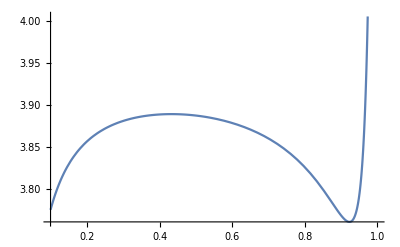

```mathematica
Plot[(-2+3 g+g y+(e^2 (-3+y+g (1+g+y-g y)))/(e (-1+g)-g ϵ)+((-1+e)^2 (3-g (1+g)-y+(-1+g) g y))/(1+e (-1+g)-g ϵ)+((-1+e)^3 (-1+g) (-1+y))/(-1+e-e g+g ϵ)^2-(e^3 (-1+g) (-1+y))/(e-e g+g ϵ)^2)/g/.{y->0.9,ϵ->0.9802,e->0.01},{g,0.1,1}]
```

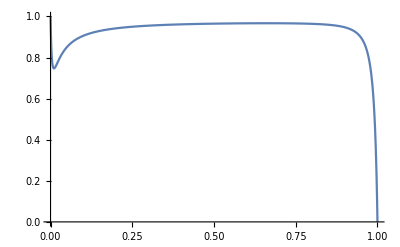

```mathematica
Plot[Evaluate[1-g*D[ϵ*Pcg+(1-ϵ)*Pdg,g]-(1-g)*D[(1-e)*Pdg+e*Pcg]/.{y->0.4,ϵ->0.9802,e->0.01}],{g,0,1},PlotRange->All]
```

```mathematica
Together[1-g*D[ϵ*Pcg+(1-ϵ)*Pdg,g]-(1-g)*D[(1-e)*Pdg+e*Pcg]]
```

1/((-e+e g-g ϵ)^2 (1-e+e g-g ϵ)^2)(e^2-2 e^3+e^4-4 e^2 g+9 e^3 g-5 e^4 g+6 e^2 g^2-15 e^3 g^2+10 e^4 g^2-4 e^2 g^3+12 e^3 g^3-10 e^4 g^3+e^2 g^4-5 e^3 g^4+5 e^4 g^4+e^3 g^5-e^4 g^5+2 e g ϵ-4 e^2 g ϵ+2 e^3 g ϵ-6 e g^2 ϵ+14 e^2 g^2 ϵ-10 e^3 g^2 ϵ+6 e g^3 ϵ-17 e^2 g^3 ϵ+16 e^3 g^3 ϵ-2 e g^4 ϵ+10 e^2 g^4 ϵ-10 e^3 g^4 ϵ-3 e^2 g^5 ϵ+2 e^3 g^5 ϵ-e g ϵ^2+e^2 g ϵ^2+g^2 ϵ^2-e g^2 ϵ^2+e^2 g^2 ϵ^2-2 g^3 ϵ^2+4 e g^3 ϵ^2-7 e^2 g^3 ϵ^2+g^4 ϵ^2-5 e g^4 ϵ^2+5 e^2 g^4 ϵ^2+3 e g^5 ϵ^2+g^3 ϵ^3+2 e g^3 ϵ^3-g^5 ϵ^3-2 e g^5 ϵ^3-g^3 ϵ^4+g^5 ϵ^4)

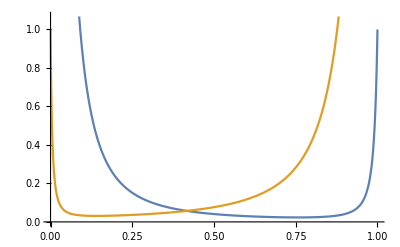

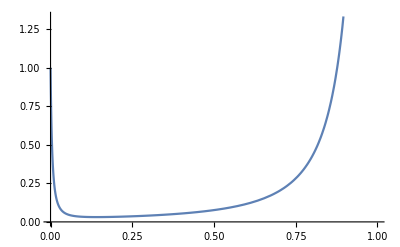

```mathematica
Plot[{Evaluate[D[ϵ*Pcg+(1-ϵ)*Pdg,g]/.{y->0.4,ϵ->0.9802,e->0.01}],Evaluate[D[(1-e)*Pdg+e*Pcg,g]/.{y->0.4,ϵ->0.9802,e->0.01}]},{g,0,1}]
Plot[Evaluate[D[(1-e)*Pdg+e*Pcg,g]/.{y->0.4,ϵ->0.9802,e->0.01}],{g,0,1}]
```

```mathematica
FullSimplify[(e (2+e (-2+g)) (-1+g)^2+(1-2 e (-1+g)^2-2 g) g ϵ+g^3 ϵ^2)]
```

e (2+e (-2+g)) (-1+g)^2+(1-2 e (-1+g)^2-2 g) g ϵ+g^3 ϵ^2

```mathematica
FullSimplify[g2 (Qcg-Qdg)-g2 (Qcg-Qdg) y+2 g2 gy (Qcg-Qdg)^2 y^2+g ((-dQcg+dQdg) g2+(dQcg-dQdg) g2 y+2 (-dQcg+dQdg) g2 gy (Qcg-Qdg) y^2)+g2(1-y)(1-Qdg+2 gz (Qcg-Qdg) (-1+y)-dQdg y+Qdg y-2 dQdg gz (Qcg-Qdg) (-1+y) y-2 gy Qcg Qdg y^2+2 gy Qdg^2 y^2)]
```

g2 (Qcg-Qdg+(-Qcg+Qdg) y+2 gy (Qcg-Qdg)^2 y^2-(dQcg-dQdg) g (1+y (-1+2 gy (Qcg-Qdg) y))+(1-y) (1-dQdg y-2 gz (Qcg-Qdg) (-1+y) (-1+dQdg y)+Qdg (-1+y+2 gy (-Qcg+Qdg) y^2)))

```mathematica
(Qcg-Qdg)(1-y)+2 gy (Qcg-Qdg)^2 y^2
```

```mathematica
-(dQcg-dQdg) g (1+y (-1+2 gy (Qcg-Qdg) y))+(1-y) (1-dQdg y-2 gz (Qcg-Qdg) (-1+y) (-1+dQdg y)+Qdg (-1+y+2 gy (-Qcg+Qdg) y^2))
```

```mathematica
(Qcg-Qdg+(-Qcg+Qdg) y+2 gy (Qcg-Qdg)^2 y^2-(dQcg-dQdg) g (1+y (-1+2 gy (Qcg-Qdg) y))+(1-y) (1-dQdg y-2 gz (Qcg-Qdg) (-1+y) (-1+dQdg y)+Qdg (-1+y+2 gy (-Qcg+Qdg) y^2)))/.{Qcg->ϵ*Pcg+(1-ϵ)*Pdg,
Qdg->(1-e)*Pdg+e*Pcg,dQcg->D[ϵ*Pcg+(1-ϵ)*Pdg,g],dQdg->D[(1-e)*Pdg+e*Pcg,g]}
```

```mathematica
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
```

```mathematica
FullSimplify[((-dQcg+dQdg) g (1+y (-1+2 gy (Qcg-Qdg) y))+(Qcg-Qdg) (1+y (-1+2 gy (Qcg-Qdg) y))-(1-y) (-1+Qdg+dQdg y+2 gz (Qcg-Qdg) (-1+y) (-1+dQdg y)+Qdg y (-1+2 gy (Qcg-Qdg) y)))//.{dQcg->D[Qcg,g],dQdg->D[Qdg,g],Qcg->ϵ*Pcg+(1-ϵ)*Pdg,
Qdg->(1-e)*Pdg+e*Pcg}]
```

$Aborted

```mathematica
FullSimplify[1/2 (x+√(4 g2-4 g2 x+x^2-4 g2 y))/.{x->0}]
```

√(g2-g2 y)

```mathematica
Solve[(-(dQcg-dQdg) g g2 (2 gx (Qcg-Qdg) x^2+2 gy (Qcg-Qdg) y^2+(1+λ)^2-x (1+λ)^2-y (1+λ)^2)+g2 (Qcg-Qdg) (2 gx (Qcg-Qdg) x^2+2 gy (Qcg-Qdg) y^2+(1+λ)^2-x (1+λ)^2-y (1+λ)^2)+g^2 (2 Qdg^2 (gx x^2+gy y^2)-2 gz (Qcg-Qdg) (-1+x+y) (-1+dQcg x+dQdg y-λ)-(-1+dQcg x+dQdg y-λ) (1+λ)^2+Qdg (-1+x-2 gx Qcg x^2+y-2 gy Qcg y^2+2 (-1+x+y) λ+(-1+x+y) λ^2)))==0,λ]
```

```mathematica
FullSimplify[g-x*Qcg-y*Qdg-(1-x-y)*Qcg]
FullSimplify[g-x*Qcg-y*Qdg-(1-x-y)*((Qcg-Qdg)*g2/g+Qdg)]
```

((-1+g) g (-1+g+y) (e-ϵ)^2)/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

```mathematica
FullSimplify[((-1+g) (g^2-g x+g2 (-1+x+y)) (e-ϵ)^2)/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))/.{g2->g}]
```

((-1+g) g (-1+g+y) (e-ϵ)^2)/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

```mathematica
Solve[(g^2-g x+g2 (-1+x+y))==0,g]
```

{{g→1/2 (x-√(4 g2-4 g2 x+x^2-4 g2 y))},{g→1/2 (x+√(4 g2-4 g2 x+x^2-4 g2 y))}}

```mathematica
FullSimplify[4*g2-4*g2*x-4*g2*y]
```

-4 g2 (-1+x+y)

```mathematica
FullSimplify[1/2 (x-√(4 g-4 g x+x^2-4 g y))]
```

1/2 (x-√(x^2-4 g (-1+x+y)))

### Theorem A.4.6

```mathematica
(* dQdg/dg > 0 *)
D[(1-e)*Pdg+e*Pcg,g]
Together[-(e g ϵ (-e+ϵ))/(e (1-g)+g ϵ)^2+(e ϵ)/(e (1-g)+g ϵ)]
```

((1-e) (1-ϵ))/((1-e) (1-g)+g (1-ϵ))-((1-e) g (1-ϵ) (e-ϵ))/((1-e) (1-g)+g (1-ϵ))^2-(e g ϵ (-e+ϵ))/(e (1-g)+g ϵ)^2+(e ϵ)/(e (1-g)+g ϵ)

(e^2 ϵ)/(-e+e g-g ϵ)^2

```mathematica
(* g - Qdg > 0 *)
FullSimplify[Together[g-(1-e)*Pdg-e*Pcg]]
```

((-1+g) g^2 (e-ϵ)^2)/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

### Numerical convergence

```mathematica
(* Public *)
M=Array[m,{24*2,2}];
e1=0.01;
e=0.01;
ϵ=(1-e1)*(1-e)+e1*e;
Do[
z=0.01*i;
{fy,fz}={Qdg-gy,Qcg-gz}//.{g->(1-z)*gy+z*gz};
geq=Select[g/.Solve[g==Qcg*z+Qdg*(1-z),g],0<#<1&][[1]];
{gyeq,gzeq}={Qdg,Qcg}/.{g->geq};
eigs=Eigenvalues[D[{fy,fz},{{gy,gz}}]/.{gy->gyeq,gz->gzeq}];
M[[i/4]]={z,eigs[[1]]};
M[[i/4+24]]={z,eigs[[2]]};
,{i,4,96,4}]
eigenImage=ListPlot[M,LabelStyle->"20",ImageSize->Large,PlotStyle->{Directive[Blue,PointSize[Large]]},PlotMarkers->Automatic,BaseStyle->{FontSize->28},PlotRange->{{0,1},{-1.005,-0.8}},Frame->{{True,True},{True,True}},FrameStyle->{{Black,Black},{Black,Black}},AspectRatio->1,FrameLabel->{Framed[Style["Discriminators, z"],FrameStyle->None],"Eigenvalues"}];
Export["eigen_St_public.pdf",eigenImage];
```

```mathematica
Clear["Global`*"]
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
{fy,fz}={Qdg-gy,Qcg-gz//.{g->(1-z)*gy+z*gz}};
Solve[g==Qcg*z+Qdg*(1-z),g]
{gyeq,gzeq}={Qdg,Qcg}/.{g->z}
FullSimplify[Eigenvalues[D[{fy,fz},{{gy,gz}}]//.{gy->gyeq,gz->gzeq}]]
```

{{g→0},{g→1},{g→z}}

{((1-e) z (1-ϵ))/((1-e) (1-z)+z (1-ϵ))+(e z ϵ)/(e (1-z)+z ϵ),(z (1-ϵ)^2)/((1-e) (1-z)+z (1-ϵ))+(z ϵ^2)/(e (1-z)+z ϵ)}

{-1,1/((-1+e-e z+z ϵ)^2 (e-e z+z ϵ)^2)(-1+z) (-e^2 (-1+z) (1-z+e (-2+e (-1+z)^2+3 z))+2 e z (1-z+e (-2+3 z+e (-1+z) (-1+2 z))) ϵ+z (z+e (-1+e+3 (-1+e) z-6 e z^2)) ϵ^2+4 e z^3 ϵ^3-z^3 ϵ^4)}

```mathematica
-((-1+y) y (e-ϵ)^2)/((-1+e y+ϵ-y ϵ) (e y+ϵ-y ϵ))/.{y->0.6}
```

-0.939396

```mathematica
z=0.03;
{fy,fz}={Qdg-gy,Qcg-gz//.{g->(1-z)*gy+z*gz}};
geq=g/.Solve[g==Qcg*z+Qdg*(1-z),g];
{gyeq,gzeq}={Qdg,Qcg}/.{g->geq};
eigs=Eigenvalues[D[{fy,fz},{{gy,gz}}]//.{g->geq,gy->gyeq,gz->gzeq}]
```

Eigenvalues[{{-1,0},{{93.1972,6.09457,0.97},{1.88239,-0.811508,-0.97}}}]

```mathematica
geq=g/.Solve[g==Qcg*z+Qdg*(1-z),g]
```

{0.,0.03,1.}

```mathematica
z=0.4;
{fy,fz}={Qdg-gy,Qcg-gz//.{g->(1-z)*gy+z*gz}};
Solve[g==Qcg*z+Qdg*(1-z),g]
{gyeq,gzeq}={Qdg,Qcg}/.{g->z}
Eigenvalues[D[{fy,fz},{{gy,gz}}]//.{gy->gyeq,gz->gzeq}]
```

{{g→0.},{g→0.4},{g→1.}}

{0.0228756,0.965687}

{-1.,-0.975319}

```mathematica
Eigenvalues[D[{fy,fz},{{gy,gz}}]//.{g->geq,gy->gyeq,gz->gzeq}]
```

```mathematica
-((-1+y) y (e-ϵ)^2)/((-1+e y+ϵ-y ϵ) (e y+ϵ-y ϵ))/.{y->0.7}
```

-0.939396

```mathematica
M
```

{{0.04,-1.},{0.08,-1.},{0.12,-1.},{0.16,-1.},{0.2,-1.},{0.24,-1.},{0.28,-1.},{0.32,-1.},{0.36,-1.},{0.4,-1.},{0.44,-1.},{0.48,-1.},{0.52,-1.},{0.56,-1.},{0.6,-1.},{0.64,-1.},{0.68,-1.},{0.72,-1.},{0.76,-1.},{0.8,-1.},{0.84,-1.},{0.88,-1.},{0.92,-1.},{0.96,-1.},{0.04,-0.0600913},{0.08,-0.0331943},{0.12,-0.0277746},{0.16,-0.0264087},{0.2,-0.0263879},{0.24,-0.0269898},{0.28,-0.0279668},{0.32,-0.0292262},{0.36,-0.030739},{0.4,-0.0325084},{0.44,-0.0345592},{0.48,-0.0369342},{0.52,-0.0396967},{0.56,-0.0429346},{0.6,-0.0467703},{0.64,-0.0513767},{0.68,-0.0570028},{0.72,-0.0640204},{0.76,-0.0730072},{0.8,-0.0849083},{0.84,-0.101372},{0.88,-0.125506},{0.92,-0.163603},{0.96,-0.225991}}

```mathematica
(* Private *)
M=Array[m,{24*2,2}];
e1=1/100;
e=1/100;
ϵ=(1-e1)*(1-e)+e1*e;
Do[
z=i/100;
g=(1-z)*gy+z*gz;
g2=(1-z)*gy2^2+z*gz2^2;
{fy,fz,fy2,fz2}={g*(Qdg-gy),(Qcg-Qdg)*g2+Qdg*g-gz*g,g*(gy^2-gy2),g*(gz^2-gz2)};
{gyeq,gzeq}=Select[Round[{gy,gz}/.Solve[{Qdg== gy,(Qcg-Qdg)*((1-z)gy^2+z*gz^2)+Qdg*g==gz*g},{gy,gz},Reals],0.0001],0< #[[1]]≤1&&0<#[[2]]≤1&][[1]];
eigs=Eigenvalues[D[{fy,fz,fy2,fz2},{{gy,gz,gy2,gz2}}]/.{gy2->gyeq^2,gz2->gzeq^2,gy->gyeq,gz->gzeq}];M[[i/4]]={z,eigs[[1]]};
M[[i/4+24]]={z,eigs[[2]]};
,{i,4,96,4}]
eigenImage=ListPlot[M,LabelStyle->"20",ImageSize->Large,PlotStyle->{Directive[Blue,PointSize[Large]]},PlotMarkers->Automatic,BaseStyle->{FontSize->28},PlotRange->{{0,1},{-3,-0.5}},Frame->{{True,True},{True,True}},FrameStyle->{{Black,Black},{Black,Black}},AspectRatio->1,FrameLabel->{Framed[Style["Discriminators, z"],FrameStyle->None],"Eigenvalues"}];
Export["eigen_St_private.pdf",eigenImage];
```

```mathematica
M
```

{{1/25,46.5601+0. ⅈ},{2/25,44.6201},{3/25,42.6801},{4/25,40.7401+0. ⅈ},{1/5,38.8001+0. ⅈ},{6/25,36.8601},{7/25,34.9201+0. ⅈ},{8/25,32.9801+0. ⅈ},{9/25,31.0401},{2/5,29.1001},{11/25,27.1601},{12/25,25.2201},{13/25,23.28},{14/25,21.34},{3/5,19.4},{16/25,17.46},{17/25,15.52+0. ⅈ},{18/25,13.58+0. ⅈ},{19/25,11.64},{4/5,9.70002},{21/25,7.76002},{22/25,5.82001},{23/25,3.88001},{24/25,1.94+0. ⅈ},{1/25,-1.+9.15577×10^-9 ⅈ},{2/25,-1.},{3/25,-1.},{4/25,-1.+0. ⅈ},{1/5,-1.+0. ⅈ},{6/25,-1.},{7/25,-1.+1.79918×10^-8 ⅈ},{8/25,-1.+1.12718×10^-8 ⅈ},{9/25,-1.},{2/5,-1.},{11/25,-1.},{12/25,-1.},{13/25,-1.},{14/25,-1.},{3/5,-1.},{16/25,-1.},{17/25,-1.+1.24928×10^-8 ⅈ},{18/25,-1.+0. ⅈ},{19/25,-1.},{4/5,-1.},{21/25,-1.},{22/25,-1.},{23/25,-1.},{24/25,-1.+0. ⅈ}}

```mathematica
z=2/100;
e1=1/100;
e=1/100;
ϵ=(1-e1)*(1-e)+e1*e;
g=(1-z)*gy+z*gz;
g2=(1-z)*gy2^2+z*gz2^2;
{fy,fz,fy2,fz2}={(Qdg-gy)*g,(Qcg-Qdg)*g2+Qdg*g-gz*g,(gy^2-gy2)*g,(gz^2-gz2)*g};
Round[{gy,gz}/.Solve[{Qcg== gy,(Qcg-Qdg)*((1-z)gy^2+z*gz^2)/g+Qdg==gz},{gy,gz},Reals],0.000001]
```

{{0.,0.},{1.,1.},{-0.010515,0.509834},{0.867094,8.71534},{1.15352,-5.62096}}

```mathematica
Eigenvalues[D[{fy,fz,fy2,fz2},{{gy,gz,gy2,gz2}}]/.{gy2->0,gz2->0,gy->0,gz->0}]
```

{0,0,0,0}

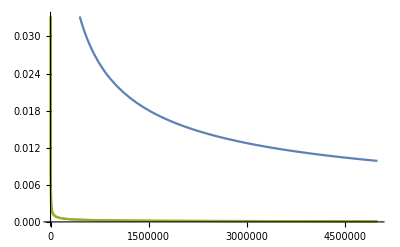

{{0.000230397,0.000235555}}

```mathematica
e1=0.01;
e2=0.01;
r=3;
ϵ=(1-e1)*(1-e2)+e1*e2;
e=e2;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Pcb=e*g/(e*g+ϵ*(1-g));
Pdb=(1-e)*g/((1-e)*g+(1-ϵ)*(1-g));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=ϵ*Pcb+(1-ϵ)*Pdb;
Qdb=(1-e)*Pdb+e*Pcb;
repsys={
gx'[t]==Qcg*g-g*gx[t],
gy'[t]==Qdg*g-g*gy[t],
gz'[t]==(Qcg-Qdg)*g2+Qdg*g-g*gz[t],
gx2'[t]==gx[t]^2-gx2[t],
gy2'[t]==gy[t]^2-gy2[t],
gz2'[t]==gz[t]^2-gz2[t]
};
R=NDSolve[Join[repsys/.{x->0,y->0.1},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{gx,gy,gz,gx2,gy2,gz2},{t,0,5000000}];
Plot[Evaluate[{gx[t],gy[t],gz[t]}/.R],{t,0,5000000}]
{gy[1000000],gz[1000000]}/.R
```

```mathematica
0.07966770396592775*(1+1/(0.8*2))
```

0.12946

```mathematica
{r*(0+gy[10000]*0.9),r*(0+gz[10000]*0.9)-(gx[10000]*0+gy[10000]*0.1+gz[10000]*0.9)}/.R
```

{{0.00715992,0.00611367}}

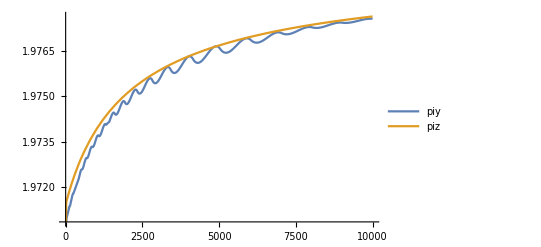

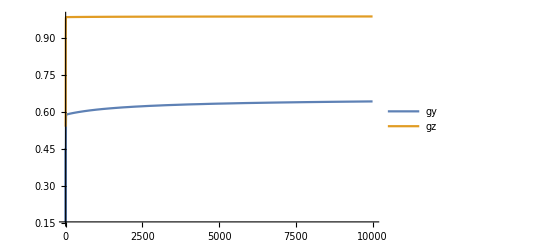

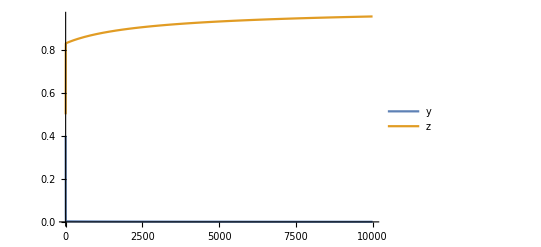

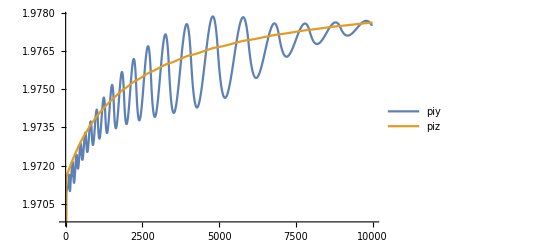

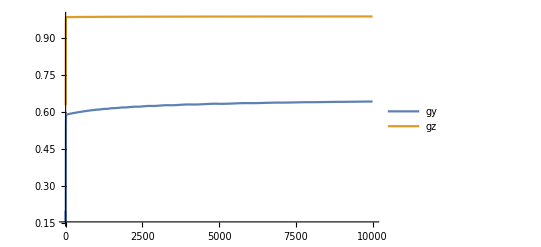

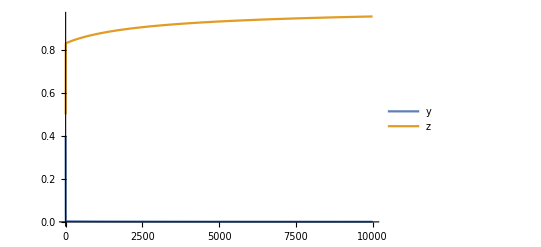

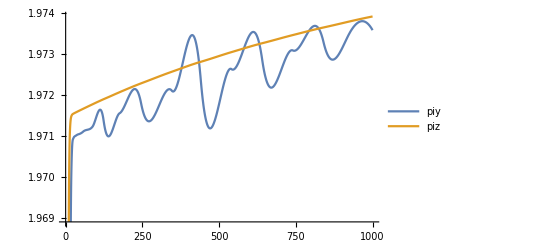

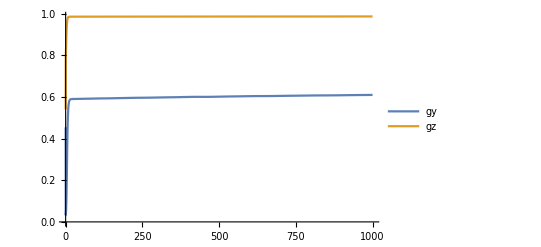

```mathematica
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(1000*(Qcg*g-g*gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(1000*(Qdg*g-g*gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(1000*((Qcg-Qdg)*g2+Qdg*g-g*gz[t])/.{x->x[t],y->y[t]}),
gx2'[t]==(1000*(gx[t]^2-gx2[t])/.{x->x[t],y->y[t]}),
gy2'[t]==(1000*(gy[t]^2-gy2[t])/.{x->x[t],y->y[t]}),
gz2'[t]==(1000*(gz[t]^2-gz2[t])/.{x->x[t],y->y[t]})
};
R=NDSolve[Join[fullsys,{x[0]==0.1,y[0]==0.4,
gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.5,gy2[0]==0.5,gz2[0]==0.5}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,10000},Method->"StiffnessSwitching"];
Plot[Evaluate[{y[t],1-x[t]-y[t]}/.R],{t,0,10000},PlotLegends->{"y","z"}]
Plot[Evaluate[{gy[t],gz[t]}/.R],{t,0,10000},PlotLegends->{"gy","gz"}]
Plot[Evaluate[{r*(x[t]+gy[t]*(1-x[t]-y[t])),r*(x[t]+gz[t]*(1-x[t]-y[t]))-(gx[t]*x[t]+gy[t]*y[t]+gz[t]*(1-x[t]-y[t]))}/.R],{t,0,10000},PlotLegends->{"piy","piz"}]
```

```mathematica
{r*(x[10000]+gy[10000]*(1-x[10000]-y[10000])),r*(x[10000]+gz[10000]*(1-x[10000]-y[10000]))-(gx[10000]*x[10000]+gy[10000]*y[10000]+gz[10000]*(1-x[10000]-y[10000]))}/.R
```

{{1.97775,1.97762}}

```mathematica
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
(* Stable equilibria *)
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(Qcg*g-g*gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(Qdg*g-g*gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*((Qcg-Qdg)*g2+Qdg*g-g*gz[t])/.{x->x[t],y->y[t]}),
gx2'[t]==(10000*(gx[t]^2-gx2[t])/.{x->x[t],y->y[t]}),
gy2'[t]==(10000*(gy[t]^2-gy2[t])/.{x->x[t],y->y[t]}),
gz2'[t]==(10000*(gz[t]^2-gz2[t])/.{x->x[t],y->y[t]})
};
R=NDSolve[Join[fullsys,{x[0]==0.001,y[0]==0.4,
gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.5,gy2[0]==0.5,gz2[0]==0.5}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,100000000},Method->"StiffnessSwitching"];
Plot[Evaluate[{gx[t],gy[t],gz[t]}/.R],{t,0,20000000}]
Plot[Evaluate[{x[t],y[t],1-x[t]-y[t]}/.R],{t,0,200},PlotLegends->{"x","y","z"}]
```

-Graphics-

-Graphics-

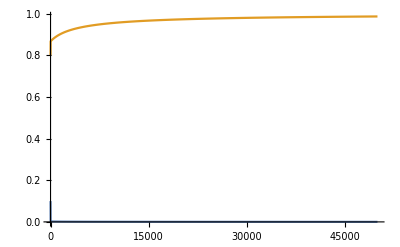

```mathematica
Plot[Evaluate[{y[t],1-x[t]-y[t]}/.R],{t,0,50000}]
```

```mathematica
{r*(x[5000000]+gy[5000000]*(1-x[5000000]-y[5000000])),r*(x[5000000]+gz[5000000]*(1-x[5000000]-y[5000000]))-(gx[5000000]*x[5000000]+gy[5000000]*y[5000000]+gz[5000000]*(1-x[5000000]-y[5000000]))}/.R
```

{{1.97944,1.97929}}

```mathematica
{y[5000000],1-x[5000000]-y[5000000]}/.R
```

{{1.79377×10^-6,0.999846}}

### Theorem

```mathematica
FullSimplify[z*g2*(Qcg-Qdg)+Qdg*g-g]
```

-((-1+g) g (e^2 (-1+2 g-g2 z)-e (-1+g+2 g ϵ-2 g2 z ϵ)+ϵ (g-g2 z ϵ)))/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

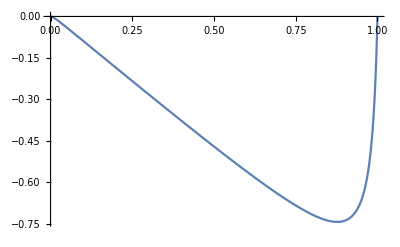

```mathematica
Plot[Evaluate[Qdg-g/.{ϵ->0.9802,e->0.01}],{g,0,1}]
```

```mathematica
FullSimplify[Solve[e^2 (-1+2 g-g2 z)-e (-1+g+2 g ϵ-2 g2 z ϵ)+ϵ (g-g2 z ϵ)==0,g]]
```

{{g→(e (-1+e+e g2 z)-2 e g2 z ϵ+g2 z ϵ^2)/((-1+2 e) (e-ϵ))}}

```mathematica
FullSimplify[-e+e^2+e^2 g2 z-2 e g2 z ϵ+g2 z ϵ^2]
```

e (-1+e+e g2 z)-2 e g2 z ϵ+g2 z ϵ^2

```mathematica
(-e+e^2+e^2 g2 z-2 e g2 z ϵ+g2 z ϵ^2)/((-1+2 e) (e-ϵ))/.{g2->1,z->1,ϵ->0.9802,e->0.01}
```

0.979588

```mathematica
FullSimplify[Solve[e^2 (-1+2 g-g z)-e (-1+g+2 g ϵ-2 g z ϵ)+ϵ (g-g z ϵ)==0,g]]
```

{{g→-((-1+e) e)/((e-ϵ) (1+e (-2+z)-z ϵ))}}

```mathematica
Collect[e^2 (-1+2 g-g2 z)-e (-1+g+2 g ϵ-2 g2 z ϵ)+ϵ (g-g2 z ϵ),g2]
```

e-e^2-e g+2 e^2 g+g ϵ-2 e g ϵ+g2 (-e^2 z+2 e z ϵ-z ϵ^2)

```mathematica
FullSimplify[Solve[e^2 (-1+2 g-g^2 z)-e (-1+g+2 g ϵ-2 g^2 z ϵ)+ϵ (g-g^2 z ϵ)==0,g]]
```

{{g→(e (-1+2 e-2 ϵ)+√(-(-1+4 (-1+e) e (-1+z)) (e-ϵ)^2)+ϵ)/(2 z (e-ϵ)^2)},{g→(e (-1+2 e-2 ϵ)-√(-(-1+4 (-1+e) e (-1+z)) (e-ϵ)^2)+ϵ)/(2 z (e-ϵ)^2)}}

```mathematica
FullSimplify[(e (-1+2 e-2 ϵ)+ϵ)^2-(-(-1+4 (-1+e) e (-1+z)) (e-ϵ)^2)]
```

4 (-1+e) e z (e-ϵ)^2

```mathematica
-2 (-1+2 (-1+e) e (-2+z)) (e-ϵ)^2/.{z->0.3,ϵ->0.9802,e->0.01}
```

1.81921

```mathematica
FullSimplify[-(-1+4 (-1+e) e (-1+z)) (e-ϵ)^2/.{z->0.3,ϵ->0.9802,e->0.01}]
```

0.915196

```mathematica
FullSimplify[(e (-1+2 e-2 ϵ)+(ϵ-e)+ϵ)/(2 z (e-ϵ)^2)]
```

```mathematica
FullSimplify[(-1+e)/(z (e-ϵ))/.{ϵ->(1-e)*(1-e1)+e*e1}]
```

```mathematica
(1-e)/(1-2 e -e1 +2 e e1)
```

```mathematica
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
g=x*gx+y*gy+(1-x-y)*gz;
g2=x*gx2^2+y*gy2^2+(1-x-y)*gz2^2;
{fx,fy,fz,fx2,fy2,fz2}={g*(Qcg-gx),g*(Qdg-gy),(Qcg-Qdg)*g2+Qdg*g-gz*g,g*(gx^2-gx2),g*(gy^2-gy2),g*(gz^2-gz2)};
eigs=Eigenvalues[D[{x*(pix-pi),y*(piy-pi),fx,fy,fz,fx2,fy2,fz2},{{x,y,gx,gy,gz,gx2,gy2,gz2}}]/.{x->0,gx2->0,gy2->0,gz2->0,gx->0,gy->0,gz->0}]
```

{-1,0,0,0,0,0,0,0}

## Stern Judging

```mathematica
Clear["Global`*"]
(*-1+Qcg+dQdb (-1+g) (-1+x)+Qdb (-1+x)-(dQcb (-1+g)+Qcb) x+dQdg g y-Qcg y+Qdg y+dQcg (g-g y)*)

gx=Qcg*g+Qcb*(1-g);
gy=Qdg*g+Qdb*(1-g);
gz=Qcg*g+Qdb*(1-g);
FullSimplify[gx*x+gy*y+gz*(1-x-y)]
sol=Solve[g==gx*x+gy*y+gz*(1-x-y),x]
FullSimplify[-(Qcg+Qdb (-1+x)-(Qcb) x-Qcg y+Qdg y)/.{x->(-g+g Qcg+Qdb-g Qdb-g Qcg y+g Qdg y)/((-1+g) (Qcb-Qdb))}]
```

Qdb+Qcb x-Qdb x+g (Qcg+Qdb (-1+x)-Qcb x-Qcg y+Qdg y)

{{x→(-g+g Qcg+Qdb-g Qdb-g Qcg y+g Qdg y)/((-1+g) (Qcb-Qdb))}}

(-g+Qcg-Qcg y+Qdg y)/(-1+g)

```mathematica
Clear["Global`*"]
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Pcb=e*g/(e*g+ϵ*(1-g));
Pdb=(1-e)*g/((1-e)*g+(1-ϵ)*(1-g));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=ϵ*Pcb+(1-ϵ)*Pdb;
Qdb=(1-e)*Pdb+e*Pcb;
```

```mathematica
FullSimplify[(-g+Qcg-Qcg y+Qdg y)/(-1+g)]
```

-(g (-1+g+y) (e-ϵ)^2)/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

### Theorem A.5.1

```mathematica
(* Show f(p) > 0 for 1/2<g<1 *)
f=FullSimplify[Qcb x+Qdb(1-x)-Qdg y-Qcg(1-y)+1-D[Qcb,g](1-g)x-D[Qdb,g](1-g)(1-x)- D[Qdg,g]g*y-D[Qcg,g]g(1-y)/.{x->((1-y)*Qcg*g+y*Qdg*g+Qdb*(1-g)-g)/((Qdb-Qcb)*(1-g))}]
p=e^4 (-1+g)^2 (1+g (-4+3 g (1+y)))-(-1+g)^2 g^2 (-2+ϵ) ϵ^2 (1+(-1+y) ϵ)+e ϵ (-1+y+g (6-2 y+g (-13-4 (-3+g) g+2 y))+ϵ+(-y+g (-6+4 y+g (10-6 g+g^2-2 (5+3 (-2+g) g) y))) ϵ+2 (-1+g)^2 g^2 ϵ^2)+e^2 ((-1+g) (-1+g (5+2 (-3+g) g-2 y))+((-1+g)^2 (1+g (-4+7 g))+(-1+2 (-1+g) g (1+3 (-1+g) g)) y) ϵ+(-(1-3 g+2 g^2)^2+y+2 (-1+g) g (2+3 (-1+g) g) y) ϵ^2)-e^3 (-1+g) (-2+g (-2 (-5+y)+g (-13+5 g+2 (-1+g) y)+2 (2 y+(-1+g) g (1+4 y)) ϵ));
{c0,c1,c2,c3,c4}=FullSimplify[CoefficientList[p,g]]
pprime=FullSimplify[D[p,g]]
FullSimplify[p/.{g->1/2}]
FullSimplify[p/.{g->1}]
FullSimplify[pprime/.{g->1/2}]
FullSimplify[pprime/.{g->1}]
```

-((g (e-ϵ)^2 (e^4 (-1+g)^2 (1+g (-4+3 g (1+y)))-(-1+g)^2 g^2 (-2+ϵ) ϵ^2 (1+(-1+y) ϵ)+e ϵ (-1+y+g (6-2 y+g (-13-4 (-3+g) g+2 y))+ϵ+(-y+g (-6+4 y+g (10-6 g+g^2-2 (5+3 (-2+g) g) y))) ϵ+2 (-1+g)^2 g^2 ϵ^2)+e^2 ((-1+g) (-1+g (5+2 (-3+g) g-2 y))+((-1+g)^2 (1+g (-4+7 g))+(-1+2 (-1+g) g (1+3 (-1+g) g)) y) ϵ+(-(1-3 g+2 g^2)^2+y+2 (-1+g) g (2+3 (-1+g) g) y) ϵ^2)-e^3 (-1+g) (-2+g (-2 (-5+y)+g (-13+5 g+2 (-1+g) y)+2 (2 y+(-1+g) g (1+4 y)) ϵ))))/((-1+e g+ϵ-g ϵ) (e g+ϵ-g ϵ) (-1+e-e g+g ϵ)^2 (e-e g+g ϵ)^2))

{(-1+e) e ((-1+e) e+(-1+y) (-1+ϵ) ϵ),-2 (-1+e) e (e-ϵ) (-3+3 e+y+3 ϵ-2 y ϵ),(e-ϵ) (3 e^3 (4+y)+e^2 (-23+(10-9 y) ϵ)+(-2+ϵ) ϵ (1+(-1+y) ϵ)+e (11-ϵ (7+3 ϵ)+y (-2+ϵ (8+ϵ)))),-2 (e-ϵ) (e^3 (5+3 y)+(-2+ϵ) ϵ (1+(-1+y) ϵ)+e (4-3 ϵ^2+y ϵ (4+ϵ))-e^2 (9-3 ϵ+y (2+5 ϵ))),(e-ϵ)^2 (-2+3 e+ϵ) (-1+e+e y+ϵ-y ϵ)}

2 (-1+2 g) (e-ϵ) (3 e^3 (-1+g) (-1+g+g y)+(-1+g) g (-2+ϵ) ϵ (1+(-1+y) ϵ)+e (3-5 g+2 g^2-y+(-3+2 y+g (1+2 g+4 (-1+g) y)) ϵ+(-1+g) g (-3+y) ϵ^2)+e^2 (-6+y+3 ϵ-2 y ϵ+g^2 (-5-2 y+ϵ-5 y ϵ)+g (11+2 y-4 ϵ+5 y ϵ)))

1/16 (-2+e+ϵ) (e+ϵ) (e+e^2 (-1+3 y)+2 e y (-2+ϵ)+ϵ (-1+ϵ-y ϵ))

(-1+e) e y (-1+ϵ) ϵ

0

-2 (-1+e) e y (e-ϵ) (-1+2 ϵ)

```mathematica
(* Show -(e+e^2(-1+3y)+2ey(-2+ϵ)+ϵ(-1+ϵ-yϵ)) =  y(ϵ-e)^2 -(1-2 e)^2(-1+e1)e1-4(-1+e)ey > 0 *)
FullSimplify[-(e+e^2 (-1+3 y)+2 e y (-2+ϵ)+ϵ (-1+ϵ-y ϵ))-y(ϵ-e)^2/.{ϵ->(1-e)(1-e1)+e*e1}]
```

-(1-2 e)^2 (-1+e1) e1-4 (-1+e) e y

```mathematica
(* Show f(p) ≤ 0 for g=1 *)
FullSimplify[1-D[Qdg,g]*y-D[Qcg,g](1-y)/.{g->1}]
```

(y (e-ϵ)^2)/((-1+ϵ) ϵ)

### Theorem A.5.2

```mathematica
(* Simplify g - x*gx - y*gy - z*gz = 0 *)
FullSimplify[g-x*(Qcg*g+Qcb*(1-g))-y*(Qdg*g+Qdb*(1-g))-(1-x-y)*(Qcg*g+Qdb*(1-g))]
(* Quadratic polynomial in the numerator p(g) *)
p =FullSimplify[Together[-((-1+g) g (e-ϵ)^2 (e (-1+g) (1-x+g (-2+2 g+x)+e (-1+g (3+g (-3+x)-2 x)+x))+e g^2 (1-e g) y-(-1+g) g (-2+2 g+2 e (-1+g) (-1+x)+x+y-2 e g y) ϵ+(-1+g) g (-1+g (1+x-y)+y) ϵ^2))/(g*(1-g)*(e-ϵ)^2 )]];
FullSimplify[CoefficientList[p,g]]
FullSimplify[p/.{g->0}]
FullSimplify[p/.{g->1/2}]
FullSimplify[p/.{g->1}]
(* Characteristic equation *)
Clear["Global`*"]
FullSimplify[CharacteristicPolynomial[{{dQcg*g*x+dQcb*(1-g)*x+(Qcg-Qcb)*x-1,dQcg*g*y+dQcb*(1-g)*y+(Qcg-Qcb)*y,dQcg*g*(1-x-y)+dQcb*(1-g)*(1-x-y)+(Qcg-Qcb)*(1-x-y)},
{dQdg*g*x+dQdb*(1-g)*x+(Qdg-Qdb)*x,dQdg*g*y+dQdb*(1-g)*y+(Qdg-Qdb)*y-1,dQdg*g*(1-x-y)+dQdb*(1-g)*(1-x-y)+(Qdg-Qdb)*(1-x-y)},
{dQcg*g*x+dQdb*(1-g)*x+(Qcg-Qdb)*x,dQcg*g*y+dQdb*(1-g)*y+(Qcg-Qdb)*y,dQcg*g*(1-x-y)+dQdb*(1-g)*(1-x-y)+(Qcg-Qdb)*(1-x-y)-1}},λ]]
```

-(((-1+g) g (e-ϵ)^2 (e (-1+g) (1-x+g (-2+2 g+x)+e (-1+g (3+g (-3+x)-2 x)+x))+e g^2 (1-e g) y-(-1+g) g (-2+2 g+2 e (-1+g) (-1+x)+x+y-2 e g y) ϵ+(-1+g) g (-1+g (1+x-y)+y) ϵ^2))/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ) (-1+e g+ϵ-g ϵ) (e g+ϵ-g ϵ)))

{e (-1+e+x-e x),e^2 (-4+3 x)+ϵ (-2+x+y+ϵ-y ϵ)+e (3+2 ϵ-2 x (1+ϵ)),-(e-ϵ) (4+3 e (-2+x)-y+2 (-1+y) ϵ-x (1+ϵ)),(e-ϵ) (2+e (-3+x-y)+(-1-x+y) ϵ)}

e (-1+e+x-e x)

-1/8 (-1+x+y) (-2+e+ϵ) (e+ϵ)

-(-1+e) e y

(-1+Qcg+dQdb (-1+g) (-1+x)+Qdb (-1+x)-(dQcb (-1+g)+Qcb) x+dQdg g y-Qcg y+Qdg y+dQcg (g-g y)-λ) (1+λ)^2

### Theorem A.5.3

```mathematica
(* Calculate Qdb - Qcb *)
FullSimplify[Qdb - Qcb]
```

((-1+g) g (e-ϵ)^2)/((-1+e g+ϵ-g ϵ) (e g+ϵ-g ϵ))

### Theorem A.5.4

```mathematica
FullSimplify[Solve[g-x*(Qcg*g+Qcb*(1-g))-y*(Qdg*g+Qdb*(1-g))-(1-x-y)*(Qcg*g+Qdb*(1-g))==0,g]/.{ϵ->0.9802,e->0.01}]
```

$Aborted

```mathematica
FullSimplify[Numerator[Together[test1+test2]]/.{g->1/2}]
```

1/256 (e-ϵ)^2 (-2+e+ϵ)^2 (e+ϵ)^2 (e (2-4 x+e (-1+3 x-3 y)+4 y)+2 (1+e (-1+x-y)) ϵ+(-1-x+y) ϵ^2)

```mathematica
x->(-g+gz-gz y+Qdb y-g Qdb y+g Qdg y)/(gz-g Qcg-Qdb+g Qdb)
```

-(g (-1+g+y) (e-ϵ)^2)/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

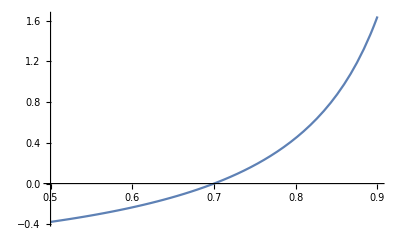

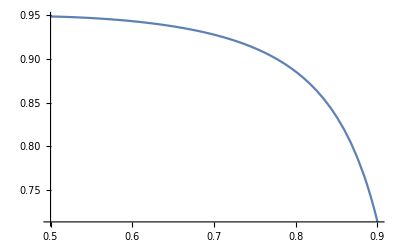

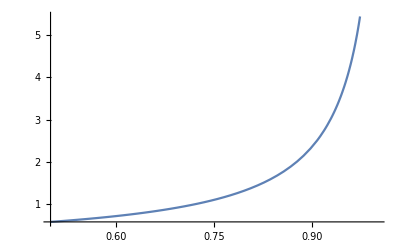

```mathematica
(* Calculate Qdb - Qcb *)
gx=Qcg*g+Qcb*(1-g);
gy=Qdg*g+Qdb*(1-g);
gx=Qcg*g+Qdb*(1-g);
test1=FullSimplify[-(Qcg+Qdb (-1+x)-(Qcb) x-Qcg y+Qdg y)/.{x->(-g+g Qcg+Qdb-g Qdb-g Qcg y+g Qdg y)/((-1+g) (Qcb-Qdb))}]
test2=-(-1+D[Qdb,g] (-1+g) (-1+x)-(D[Qcb,g] (-1+g)) x+D[Qdg,g] g y+D[Qcg,g] (g-g y))/.{x->(-g+g Qcg+Qdb-g Qdb-g Qcg y+g Qdg y)/((-1+g) (Qcb-Qdb))};
test3=-(Qcg+Qdb (-1+x)-(Qcb) x-Qcg y+Qdg y);
test4=-(-1+D[Qdb,g] (-1+g) (-1+x)-(D[Qcb,g] (-1+g)) x+D[Qdg,g] g y+D[Qcg,g] (g-g y));
Plot[test1/.{ϵ->0.9802,e->0.01,x->0.6,y->0.3},{g,0.5,0.9}]
Plot[test2/.{ϵ->0.9802,e->0.01,x->0.6,y->0.3},{g,0.5,0.9}]
Plot[test1+test2/.{ϵ->0.9802,e->0.01,x->0.6,y->0.3},{g,0.5,1}]
```

```mathematica
FullSimplify[test1+test2]
```

-((g (e-ϵ)^2 (e^4 (-1+g)^2 (1+g (-4+3 g (1+y)))-(-1+g)^2 g^2 (-2+ϵ) ϵ^2 (1+(-1+y) ϵ)+e ϵ (-1+y+g (6-2 y+g (-13-4 (-3+g) g+2 y))+ϵ+(-y+g (-6+4 y+g (10-6 g+g^2-2 (5+3 (-2+g) g) y))) ϵ+2 (-1+g)^2 g^2 ϵ^2)+e^2 ((-1+g) (-1+g (5+2 (-3+g) g-2 y))+((-1+g)^2 (1+g (-4+7 g))+(-1+2 (-1+g) g (1+3 (-1+g) g)) y) ϵ+(-(1-3 g+2 g^2)^2+y+2 (-1+g) g (2+3 (-1+g) g) y) ϵ^2)-e^3 (-1+g) (-2+g (-2 (-5+y)+g (-13+5 g+2 (-1+g) y)+2 (2 y+(-1+g) g (1+4 y)) ϵ))))/((-1+e g+ϵ-g ϵ) (e g+ϵ-g ϵ) (-1+e-e g+g ϵ)^2 (e-e g+g ϵ)^2))

```mathematica
FullSimplify[test1+test2/.{g->1/2}]
FullSimplify[test1+test2/.{g->1}]
FullSimplify[D[test1+test2,g]/.{g->1/2}]
```

-(2 (e-ϵ)^2 (e+e^2 (-1+3 y)+2 e y (-2+ϵ)+ϵ (-1+ϵ-y ϵ)))/((-2+e+ϵ)^2 (e+ϵ)^2)

Indeterminate

-(4 (e-ϵ)^2 (3 e^2+2 e (-2+ϵ)-ϵ^2) (e+e^2 (-1+3 y)+2 e y (-2+ϵ)+ϵ (-1+ϵ-y ϵ)))/((-2+e+ϵ)^3 (e+ϵ)^3)

```mathematica
(* Calculate Qdb - Qcb *)
Solve[Qdg*g + Qdb*(1-g)==g,g]
```

{{g→0},{g→1/2},{g→1},{g→(-e+2 e^2+ϵ-2 e ϵ-√(-3 e^2+8 e^3-4 e^4+2 e ϵ-4 e^2 ϵ+ϵ^2-4 e ϵ^2+4 e^2 ϵ^2))/(2 (-e+2 e^2+ϵ-2 e ϵ))},{g→(-e+2 e^2+ϵ-2 e ϵ+√(-3 e^2+8 e^3-4 e^4+2 e ϵ-4 e^2 ϵ+ϵ^2-4 e ϵ^2+4 e^2 ϵ^2))/(2 (-e+2 e^2+ϵ-2 e ϵ))}}

```mathematica
(* Calculate Qdb - Qcb *)
Solve[Qcg*g + Qdb*(1-g)==g,g]
```

{{g→0},{g→1},{g→1},{g→(-2 e+3 e^2+2 ϵ-2 e ϵ-ϵ^2-√(-4 (-e+e^2) (-2 e+3 e^2+2 ϵ-2 e ϵ-ϵ^2)+(2 e-3 e^2-2 ϵ+2 e ϵ+ϵ^2)^2))/(2 (-2 e+3 e^2+2 ϵ-2 e ϵ-ϵ^2))},{g→(-2 e+3 e^2+2 ϵ-2 e ϵ-ϵ^2+√(-4 (-e+e^2) (-2 e+3 e^2+2 ϵ-2 e ϵ-ϵ^2)+(2 e-3 e^2-2 ϵ+2 e ϵ+ϵ^2)^2))/(2 (-2 e+3 e^2+2 ϵ-2 e ϵ-ϵ^2))}}

```mathematica
(* Calculate Qdb - Qcb *)
Solve[Qcg*g + Qcb*(1-g)==g,g]
```

{{g→0},{g→0},{g→1/2},{g→1},{g→1}}

```mathematica
FullSimplify[-(g (-e^3+e^4+4 e^3 g-5 e^4 g-6 e^3 g^2+10 e^4 g^2+5 e^3 g^3-10 e^4 g^3-2 e^3 g^4+4 e^4 g^4+2 e^2 ϵ-2 e^3 ϵ-9 e^2 g ϵ+12 e^3 g ϵ+16 e^2 g^2 ϵ-28 e^3 g^2 ϵ-15 e^2 g^3 ϵ+30 e^3 g^3 ϵ+6 e^2 g^4 ϵ-12 e^3 g^4 ϵ-e ϵ^2+e^2 ϵ^2+6 e g ϵ^2-9 e^2 g ϵ^2-14 e g^2 ϵ^2+26 e^2 g^2 ϵ^2+15 e g^3 ϵ^2-30 e^2 g^3 ϵ^2-6 e g^4 ϵ^2+12 e^2 g^4 ϵ^2-g ϵ^3+2 e g ϵ^3+4 g^2 ϵ^3-8 e g^2 ϵ^3-5 g^3 ϵ^3+10 e g^3 ϵ^3+2 g^4 ϵ^3-4 e g^4 ϵ^3))]
```

-(-1+g) g (-1+2 g) (e-ϵ)^2 (e (-1+e+g+2 e (-1+g) g-g^2)-(-1+2 e) (-1+g) g ϵ)

```mathematica
Solve[e (-1+e+g+2 e (-1+g) g-g^2)-(-1+2 e) (-1+g) g ϵ==0,g]
```

{{g→(-e+2 e^2+ϵ-2 e ϵ-√(-3 e^2+8 e^3-4 e^4+2 e ϵ-4 e^2 ϵ+ϵ^2-4 e ϵ^2+4 e^2 ϵ^2))/(2 (-e+2 e^2+ϵ-2 e ϵ))},{g→(-e+2 e^2+ϵ-2 e ϵ+√(-3 e^2+8 e^3-4 e^4+2 e ϵ-4 e^2 ϵ+ϵ^2-4 e ϵ^2+4 e^2 ϵ^2))/(2 (-e+2 e^2+ϵ-2 e ϵ))}}

### Convergence

```mathematica
M=Array[m,{24*2,2}];
e1=0.01;
e=0.01;
ϵ=(1-e1)*(1-e)+e1*e;
Do[
z=0.01*i;
{fy,fz}={Qdg*g+Qdb*(1-g)-gy,Qcg*g+Qdb*(1-g)-gz//.{g->(1-z)*gy+z*gz}};
geq=Select[g/.Solve[g==Qcg*z+Qdg*(1-z),g],0<#<1&][[1]];
{gyeq,gzeq}={Qdg,Qcg}/.{g->geq};
eigs=Eigenvalues[D[{fy,fz},{{gy,gz}}]//.{g->geq,gy->gyeq,gz->gzeq}];M[[i/4]]={z,eigs[[1]]};
M[[i/4+24]]={z,eigs[[2]]};
,{i,4,96,4}]
eigenImage=ListPlot[M,LabelStyle->"20",ImageSize->Large,PlotStyle->{Directive[Blue,PointSize[Large]]},PlotMarkers->Automatic,BaseStyle->{FontSize->28},PlotRange->{{0,1},{-1.005,-0.8}},Frame->{{True,True},{True,True}},FrameStyle->{{Black,Black},{Black,Black}},AspectRatio->1,FrameLabel->{Framed[Style["Discriminators, z"],FrameStyle->None],"Eigenvalues"}];
Export["eigen_SJ_public.pdf",eigenImage];
```

### test

```mathematica
(* Calculate (dQcg/dg)*z + (dQdg/dg)*(1-z) - 1 *)
FullSimplify[Qdg*(1-z)+Qcg*z-1/.{z->(g-Qdg*g-Qdb*(1-g))/(g*Qcg-g*Qdg)}]
```

```mathematica
(* Calculate dQdb/dg - 1 *)
FullSimplify[D[Qdb,g] - 1]
```

## Public assessment: Theorem A.3.2

```mathematica
Clear["Global`*"]
```

```mathematica
eq=FullSimplify[Solve[g*Qdg*(1-z)+z*g*Qcg+1-g==g,g]][[2]]
```

{g→-(3 e^2+ϵ-2 e (1+ϵ)+√(e^3 (4-3 e+4 (-1+e) z)+2 e^2 (-3+2 e+4 z-4 e z) ϵ+(1+4 (-1+e) e z) ϵ^2))/(2 (e-ϵ) (1+e (-3+z)+ϵ-z ϵ))}

```mathematica
(Q\cg-Q\dg)(g-g_2)z=g(Q\cg-2)+1
```

```mathematica
FullSimplify[g*Qdg*(1-z)+z*g*Qcg+1-2*g]
```

((-1+g) (e^2 (-1+g (3+g (-3+z)))+e ((-1+g)^2-2 g (1+g (-2+z)) ϵ)+g ϵ (1+g (-1+(-1+z) ϵ))))/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

```mathematica
Collect[(e^2 (-1+g (3+g (-3+z)))+e ((-1+g)^2-2 g (1+g (-2+z)) ϵ)+g ϵ (1+g (-1+(-1+z) ϵ))),g]
```

e-e^2+g (-2 e+3 e^2+ϵ-2 e ϵ)+g^2 (e+e^2 (-3+z)-2 e (-2+z) ϵ+ϵ (-1+(-1+z) ϵ))

```mathematica
condition=FullSimplify[D[Qdg,g]*(1-z)-g/.{g->1}]
```

(e^2 (-1+z)-2 e (-1+z) ϵ+(z-ϵ) ϵ)/((-1+ϵ) ϵ)

```mathematica
FullSimplify[D[Qdg,g]*(1-z)+D[Qcg,g]*z-1/.{g->1}]
```

```mathematica
TeXForm[((-1+z) (e-ϵ)^2)/((-1+ϵ) ϵ)]
```

\frac{(z-1) (e-\epsilon )^2}{(\epsilon -1) \epsilon }

```mathematica
Collect[e^2 (1+g (-4-3 (-2+g) g))+g (-1+g (2+g (-2+ϵ))) ϵ+e (-1+g) (1+2 (-1+g) g (1+ϵ)),g]
```

```mathematica
Collect[e^2 (1+g (-4-3 (-2+g) g))+g (-1+g (2+g (-2+ϵ))) ϵ+e (-1+g) (1+2 (-1+g) g (1+ϵ))/.{g->g+δ},g]
```

```mathematica
FullSimplify[-e+e^2+e δ-4 e^2 δ+6 e^2 δ^2-3 e^2 δ^3-δ ϵ+2 δ^2 ϵ+δ^3 (-2+ϵ) ϵ+2 e δ (1+ϵ)-4 e δ^2 (1+ϵ)+2 e δ^3 (1+ϵ)+g^3 (-3 e^2+(-2+ϵ) ϵ+2 e (1+ϵ))+g^2 (6 e^2-9 e^2 δ+2 ϵ+3 δ (-2+ϵ) ϵ-4 e (1+ϵ)+6 e δ (1+ϵ))+g (e-4 e^2+12 e^2 δ-9 e^2 δ^2-ϵ+4 δ ϵ+3 δ^2 (-2+ϵ) ϵ+2 e (1+ϵ)-8 e δ (1+ϵ)+6 e δ^2 (1+ϵ))-(e^2 (1+g (-4-3 (-2+g) g))+g (-1+g (2+g (-2+ϵ))) ϵ+e (-1+g) (1+2 (-1+g) g (1+ϵ)))]
```

```mathematica
Collect[δ (-e^2 (4+9 g^2+3 (-2+δ) δ+3 g (-4+3 δ))+(-1+δ (2+δ (-2+ϵ))+g (4+3 δ (-2+ϵ))+3 g^2 (-2+ϵ)) ϵ+e (3+2 ϵ+6 g^2 (1+ϵ)+2 (-2+δ) δ (1+ϵ)+2 g (-4+3 δ) (1+ϵ))),δ]
```

δ^3 (-3 e^2+(-2+ϵ) ϵ+2 e (1+ϵ))+δ^2 (6 e^2-9 e^2 g+2 ϵ+3 g (-2+ϵ) ϵ-4 e (1+ϵ)+6 e g (1+ϵ))+δ (3 e-4 e^2+12 e^2 g-9 e^2 g^2-ϵ+2 e ϵ+4 g ϵ+3 g^2 (-2+ϵ) ϵ-8 e g (1+ϵ)+6 e g^2 (1+ϵ))

```mathematica
FullSimplify[3 e-4 e^2+12 e^2 g-9 e^2 g^2-ϵ+2 e ϵ+4 g ϵ+3 g^2 (-2+ϵ) ϵ-8 e g (1+ϵ)+6 e g^2 (1+ϵ)]
```

```mathematica
Assuming[1>g>0&&1>ϵ>0.5>e>0&&1>e1>0&&ϵ==(1-e)*(1-e1)+e*e1&&1>z>0,FullSimplify@Reduce[e^2 (-1+z)-2 e (-1+z) ϵ+(z-ϵ) ϵ< 0]]
```

z<(e-ϵ)^2/(e^2+ϵ-2 e ϵ)

```mathematica
Assuming[1>g>0&&1>ϵ>0.5>e>0&&1>e1>0&&ϵ==(1-e)*(1-e1)+e*e1&&1>z>0,FullSimplify@Reduce[(12 e^2+4 ϵ-8 e (1+ϵ))≤0]]
```

3 e^2+ϵ≤2 e (1+ϵ)

```mathematica
eq5=FullSimplify[D[Qdg,g]*(1-z)+D[Qcg,g]*z-1]
```

-((e-ϵ)^2 (e^2 (-1+g)^2 ((-2+g) g+z)+g^2 ϵ (1-2 g+z+g^2 ϵ-z ϵ)-e (-1+g)^2 (z+2 g (-1+g ϵ))))/((-1+e-e g+g ϵ)^2 (e-e g+g ϵ)^2)

```mathematica
FullSimplify[D[Qdg,g]*(1-z)+D[Qcg,g]*z-g/.{g->1}]
```

((-1+z) (e-ϵ)^2)/((-1+ϵ) ϵ)

```mathematica
Assuming[1>ϵ>0.5>e>0&&1>e1>0&&ϵ==(1-e)*(1-e1)+e*e1&&1>z>0,FullSimplify@Reduce[(-e^2 (1+z)+2 e (1+z) ϵ+ϵ (z-ϵ-2 z ϵ))/((-1+ϵ) ϵ)>0]]
```

1+2 e+√(1-4 (-1+e) e)==4 ϵ||(z>-(e-ϵ)^2/(e^2-2 e ϵ+ϵ (-1+2 ϵ))&&1+2 e+√(1-4 (-1+e) e)<4 ϵ)||(z<-(e-ϵ)^2/(e^2-2 e ϵ+ϵ (-1+2 ϵ))&&1+2 e+√(1-4 (-1+e) e)>4 ϵ)

```mathematica
FullSimplify[g*Qdg*(1-z)+z*g*Qcg+1-2*g]
```

((-1+g) (e^2 (-1+g (3+g (-3+z)))+e ((-1+g)^2-2 g (1+g (-2+z)) ϵ)+g ϵ (1+g (-1+(-1+z) ϵ))))/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

```mathematica
Assuming[1>g>0&&1>ϵ>0.5>e>0&&1>e1>0&&ϵ==(1-e)*(1-e1)+e*e1&&1>z>0,FullSimplify@Reduce[(-4 e+6 e^2+2 ϵ-4 e ϵ+√(-2 e^2+3 e^3+8 e ϵ-7 e^2 ϵ-6 e^3 ϵ-2 ϵ^2-7 e ϵ^2+16 e^2 ϵ^2+3 ϵ^3-6 e ϵ^3))/(3 (-2 e+3 e^2+2 ϵ-2 e ϵ-ϵ^2))≤0]]
```

ϵ≥Root[2 e^2-3 e^3+(-8 e+7 e^2+6 e^3) #1+(2+7 e-16 e^2) #1^2+(-3+6 e) #1^3&,3]&&√(21 (-11+8 √2))+14 e>7

```mathematica
Solve[3 e-4 e^2+12 e^2 g-9 e^2 g^2-ϵ+2 e ϵ+4 g ϵ+3 g^2 (-2+ϵ) ϵ-8 e g (1+ϵ)+6 e g^2 (1+ϵ)==0,g]
```

{{g→(-4 e+6 e^2+2 ϵ-4 e ϵ-√(-2 e^2+3 e^3+8 e ϵ-7 e^2 ϵ-6 e^3 ϵ-2 ϵ^2-7 e ϵ^2+16 e^2 ϵ^2+3 ϵ^3-6 e ϵ^3))/(3 (-2 e+3 e^2+2 ϵ-2 e ϵ-ϵ^2))},{g→(-4 e+6 e^2+2 ϵ-4 e ϵ+√(-2 e^2+3 e^3+8 e ϵ-7 e^2 ϵ-6 e^3 ϵ-2 ϵ^2-7 e ϵ^2+16 e^2 ϵ^2+3 ϵ^3-6 e ϵ^3))/(3 (-2 e+3 e^2+2 ϵ-2 e ϵ-ϵ^2))}}

```mathematica
Collect[-e^2 (2-3 g)^2+(-1+g (4+3 g (-2+ϵ))) ϵ+e (3+2 ϵ+2 g (-4+3 g) (1+ϵ)),g]
```

3 e-4 e^2-ϵ+2 e ϵ+g (12 e^2+4 ϵ-8 e (1+ϵ))+g^2 (-9 e^2+3 (-2+ϵ) ϵ+6 e (1+ϵ))

```mathematica
FullSimplify[Together[3 e-4 e^2-ϵ+2 e ϵ]]
```

(e^2 (1+g (-4-3 (-2+g) g))+g (-1+g (2+g (-2+ϵ))) ϵ+e (-1+g) (1+2 (-1+g) g (1+ϵ)))/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ))

```mathematica
Solve[Qdg*g+1-2*g==0,g]
```

{{g→1},{g→(-2 e+3 e^2+ϵ-2 e ϵ-√(4 e^3-3 e^4-6 e^2 ϵ+4 e^3 ϵ+ϵ^2))/(2 (-e+3 e^2+ϵ-4 e ϵ+ϵ^2))},{g→(-2 e+3 e^2+ϵ-2 e ϵ+√(4 e^3-3 e^4-6 e^2 ϵ+4 e^3 ϵ+ϵ^2))/(2 (-e+3 e^2+ϵ-4 e ϵ+ϵ^2))}}

```mathematica
FullSimplify[D[Qdg,g]*(1-z)-g/.{g->1}]
```

(e^2 (-1+z)-2 e (-1+z) ϵ+(z-ϵ) ϵ)/((-1+ϵ) ϵ)

```mathematica
Assuming[1>ϵ>0.5>e>0&&1>e1>0&&ϵ==(1-e)*(1-e1)+e*e1&&1>z>0,FullSimplify@Reduce[condition≤0]]
```

$Aborted

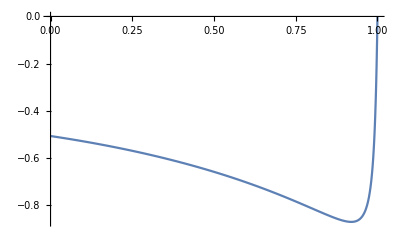

```mathematica
Plot[Evaluate[D[Qcg,g]*(z)-g/.eq/.{e->0.01,ϵ->0.98}],{z,0,1}]
```

```mathematica
Solve[1-p-θ*(1-2*p)^2==p+1/(2*θ)-θ*(p+1/(2*θ)-p)^2,p]
```

{{p→(-1+2 θ)/(4 θ)},{p→(-1+2 θ)/(4 θ)}}

```mathematica
Simplify[1-p-θ*(1-2*p)^2-(p+1/(2*θ)-θ*(p+1/(2*θ)-p)^2)]
```

-(1+(-2+4 p) θ)^2/(4 θ)